## Indexed DoConcatenate & algorithms to summarize networks

### Code to convert a network to/from its specification as a list of sets of integers:

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

### Musings on notation:

```mathematica
Sum[i^2,{i,1,n}]
```

```mathematica
∑_(i=1)^n i^2
```

1/6 n (1+n) (1+2 n)

```mathematica
⊎_(index=start)^end expr           ∪_(index=start)^end expr            Underoverscript[ℂ, index=start, end] expr
```

Σ_(i=1)^3 a_i=a_1+a_2+a_3

∪_(i=1)^3 S_i=S_1∪S_2∪S_3

€_(i=1)^3 S_i=S_1⧺S_2⧺S_3

‡ \[doubleplus] ⧺ €  ℂ  ⊎

```mathematica
ToCharacterCode["€⧺"]
```

{8364,10746}

```mathematica
FromCharacterCode[{8364,10746,42898,42899,580,8852,8846}]
```

€⧺ꞒꞓɄ⊔⊎

Disjoint Union, Multiset Union

### DoConcatenate (display & use reduced forms of an integer set list):

Mathematica already contains two functions to join or concatenate lists: Join and Catenate

Joinpaclet:ref/Join[list_1,list_2,…]

Catenatepaclet:ref/Catenate[{list_1,list_2,…}]

Of these, we view the first as grammatically preferable, avoiding an extra set of curly braces. There is no generally accepted symbol for concatenation. ChatGPT lists the following:

The symbol commonly used to denote concatenation in programming and mathematics varies by context and language. Here are a few examples:

Dot or Period (.): Used in many programming languages like Python and PHP.
Plus Sign (+): Often used in languages like JavaScript, Java, and C++ for string concatenation.
Double Pipe (||): Used in SQL and some other contexts.
Ampersand (&): Used in languages like Visual Basic and some shell scripting languages.
Circle Dot (⊙): Sometimes used in mathematical contexts to denote the concatenation of functions.
Each of these symbols represents the action of joining two or more strings or sequences together.

Each of the options listed has significant drawbacks.  “.”, “+”, and “&” are used in widely varying contexts. The circle dot carries a specific meaning as function composition (not concatenation), and although the double pipe “||” has an appeal from its partial acceptance as a “logical or” operator, this meaning is also not exactly the desired one. Omitted from the above list is the dedicated symbol for concatenation in the computer language Haskell, either represented as two consectutive plus signs (“++”), or a shifted overstrike, now implemented as unicode 10746 (hex 29FA): “⧺”.  In Haskell code, [1,2,3]⧺[4,5,6] results in [1,2,3,4,5,6]

In our opinion, this symbol overcomes many of the drawbacks of the others. We propose to use it as an “infix” version of the Join function. The Mathematica code,

```mathematica
{1,2,3} ~Join~ {4,5,6}
```

{1,2,3,4,5,6}

would then look like: {1,2,3} ⧺ {4,5,6}.  Join[{1,2},{3,4,5},{6}] would be written as:

{1,2}⧺{3,4,5}⧺{6}

This can be done by defining a new function, Concatenate (or simply, Cat), and specifying its DisplayForm and its executable form as follows.

```mathematica
Clear[Concatenate,Cat]
Cat=Concatenate;
Concatenate[l__List] := Join[l];
Format[Concatenate[l__]] := Row[Riffle[{l},"⧺"]];  (* FromCharacterCode[10746] *)
```

Some examples of usage:

```mathematica
Concatenate[{1,1,2,3},{3,4},{4,5,6,6}]
```

{1,1,2,3,3,4,4,5,6,6}

```mathematica
Cat[Subscript[S, 1],Subscript[S, 2],Subscript[S, 3]]
```

S_1⧺S_2⧺S_3

```mathematica
Subscript[S, 1] ~Cat~ Subscript[S, 2] ~Cat~ Subscript[S, 3]
```

S_1⧺S_2⧺S_3

What is completely lacking in Mathematica, and to our knowledge, in any mathematical or computer science context, is an indexed version of the concatenate operator.  Indexed operators are used for sums, products, and unions, among other lesser-known examples, such as disjoint unions and multiset unions. It is interesting that the most common examples, the indexed sum and the indexed product, use a different symbol from the simple operator.

∑_(i=1)^3 i=1+2+3=6

∏_(i=1)^3 i=1×2×3=6

However the simple symbol for the union of two or more sets is reused for the indexed union as well.

∪_(i=1)^3 S_i=S_1∪S_2∪S_3

As of version 13, Mathematica does not implement an indexed union, so there is no direct precedent for us.

The current need is for something other than a union or indexed union, which automatically deletes all duplicate elements and sorts the resulting list.

```mathematica
{1,1,2,3}∪{3,4}∪{4,5,6,6}
```

{1,2,3,4,5,6}

As in the unindexed version, we need to retain all duplicate elements and the order given. So we roll our own. Visually, we select a symbol that resembles a “C”, but also resembles our infix operator “⧺”.  We settled on the euro symbol.

The following implements most of the (single) iterator options allowed for functions such as Do, Table, Sum and Product.

```mathematica
Clear[DoConcatenate,DoCat];  DoCat = DoConcatenate;
Format[DoConcatenate[x__, {var_, start_, finish_}]] :=
DisplayForm[RowBox[{UnderoverscriptBox["€", RowBox[{var, "=", start}], finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];  (* FromCharacterCode[8364] *)
Format[DoConcatenate[x__, {var_, finish_}]] :=  DisplayForm[RowBox[{UnderoverscriptBox["€", var, finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];
Format[DoConcatenate[x__, finish_]] := DisplayForm[RowBox[{OverscriptBox["€", finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];
```

```mathematica
{DoCat[Subscript[S, i],{i,2,4}],DoCat[Subscript[S, i],{i,3}],DoCat[S,3]}
```

{€_(i=2)^4[S_i],€_i^3[S_i],€^3[S]}

That last case lends itself to further optional notational simplification.

```mathematica
ToDotNotation[x___] := x //. DoConcatenate[y__,finish_]:>CenterDot[finish,{y}];
FromDotNotation[x___] := x //. CenterDot[finish_,{y___}] :> DoConcatenate[y,finish]
```

```mathematica
FromDotNotation /@ {5·{{1}}, 5·{1}}
```

{€^5[{1}],€^5[1]}

```mathematica
ToDotNotation /@ %
```

{5·{{1}},5·{1}}

Now we need code to execute it, for finite cases.  Let’s require the Expand function to be applied before doing anything.

```mathematica
DoC[x__, iter:(_Integer|{_,_Integer}|{_,_Integer,_Integer})]:= Sequence @@ (Join @@ Table[{x},  iter]); 
(* allow 1 or more elements to be repeated & concatenated according to iter, result will be a subsequence, assumed to be inside a List *)
DoC[x__] := DoConcatenate[x] (* any non-resolved cases redefined, awaiting further processing *)

Unprotect[Expand,ExpandAll];
ExpandAll[x_ /; !FreeQ[x,DoConcatenate]] := (FromDotNotation[x] //. DoConcatenate->DoC);
Expand[x_ /; !FreeQ[x,DoConcatenate] ] := (x /. DoConcatenate->DoC);
Protect[Expand,ExpandAll]
```

{Expand,ExpandAll}

```mathematica
{DoCat[i,i^2,i^3,{i,4}] }
```

{€_i^4[i,i^2,i^3]}

```mathematica
Expand[%]
```

{1,1,1,2,4,8,3,9,27,4,16,64}

```mathematica
ExpandAll[%%]
```

{1,1,1,2,4,8,3,9,27,4,16,64}

```mathematica
{DoCat[{i,i^2},{i^3},{i,1,4}]}
```

{€_(i=1)^4[{i,i^2},{i^3}]}

```mathematica
Expand@%
```

{{1,1},{1},{2,4},{8},{3,9},{27},{4,16},{64}}

```mathematica
{DoCat[{1,2,3},4]}
```

{€^4[{1,2,3}]}

```mathematica
Expand@%
```

{{1,2,3},{1,2,3},{1,2,3},{1,2,3}}

The dot notation can be used for simple repetitions of sets or subsequences of sets of integers

```mathematica
Table[{1},5]
```

{{1},{1},{1},{1},{1}}

```mathematica
Table[{{1},{2}},5]
```

{{{1},{2}},{{1},{2}},{{1},{2}},{{1},{2}},{{1},{2}}}

```mathematica
{DoConcatenate[{1},5]}
```

{€^5[{1}]}

```mathematica
ToDotNotation[%]
```

{5·{{1}}}

```mathematica
FromDotNotation[%]
```

{€^5[{1}]}

```mathematica
Expand[%]
```

{{1},{1},{1},{1},{1}}

DoConcatenate objects can be nested:

```mathematica
{
DoConcatenate[
{1, 5n+4,5n+5},
DoConcatenate[n·{{1}},{1,5n+5+k},{k,1,4}],
(n-1)·{{1}},{},
{n,1,8}]
}
```

{€_(n=1)^8[{1,4+5 n,5+5 n},€_(k=1)^4[n·{{1}},{1,5+k+5 n}],(-1+n)·{{1}},{}]}

```mathematica
ExpandAll@%
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

```mathematica
Expand@%%
```

{{1,9,10},1·{{1}},{1,11},1·{{1}},{1,12},1·{{1}},{1,13},1·{{1}},{1,14},0·{{1}},{},{1,14,15},2·{{1}},{1,16},2·{{1}},{1,17},2·{{1}},{1,18},2·{{1}},{1,19},1·{{1}},{},{1,19,20},3·{{1}},{1,21},3·{{1}},{1,22},3·{{1}},{1,23},3·{{1}},{1,24},2·{{1}},{},{1,24,25},4·{{1}},{1,26},4·{{1}},{1,27},4·{{1}},{1,28},4·{{1}},{1,29},3·{{1}},{},{1,29,30},5·{{1}},{1,31},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34},4·{{1}},{},{1,34,35},6·{{1}},{1,36},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39},5·{{1}},{},{1,39,40},7·{{1}},{1,41},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44},6·{{1}},{},{1,44,45},8·{{1}},{1,46},8·{{1}},{1,47},8·{{1}},{1,48},8·{{1}},{1,49},7·{{1}},{}}

```mathematica
FromDotNotation@%
```

{{1,9,10},€^1[{1}],{1,11},€^1[{1}],{1,12},€^1[{1}],{1,13},€^1[{1}],{1,14},€^0[{1}],{},{1,14,15},€^2[{1}],{1,16},€^2[{1}],{1,17},€^2[{1}],{1,18},€^2[{1}],{1,19},€^1[{1}],{},{1,19,20},€^3[{1}],{1,21},€^3[{1}],{1,22},€^3[{1}],{1,23},€^3[{1}],{1,24},€^2[{1}],{},{1,24,25},€^4[{1}],{1,26},€^4[{1}],{1,27},€^4[{1}],{1,28},€^4[{1}],{1,29},€^3[{1}],{},{1,29,30},€^5[{1}],{1,31},€^5[{1}],{1,32},€^5[{1}],{1,33},€^5[{1}],{1,34},€^4[{1}],{},{1,34,35},€^6[{1}],{1,36},€^6[{1}],{1,37},€^6[{1}],{1,38},€^6[{1}],{1,39},€^5[{1}],{},{1,39,40},€^7[{1}],{1,41},€^7[{1}],{1,42},€^7[{1}],{1,43},€^7[{1}],{1,44},€^6[{1}],{},{1,44,45},€^8[{1}],{1,46},€^8[{1}],{1,47},€^8[{1}],{1,48},€^8[{1}],{1,49},€^7[{1}],{}}

```mathematica
Expand@%
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

This integer set list describes the following network:

```mathematica
FromNetDifferenceSets[%24]
```

{1→2,1→10,1→11,2→3,3→4,3→14,4→5,5→6,5→17,6→7,7→8,7→20,8→9,9→10,9→23,11→12,11→25,11→26,12→13,13→14,14→15,14→30,15→16,16→17,17→18,17→34,18→19,19→20,20→21,20→38,21→22,22→23,23→24,23→42,24→25,26→27,26→45,26→46,27→28,28→29,29→30,30→31,30→51,31→32,32→33,33→34,34→35,34→56,35→36,36→37,37→38,38→39,38→61,39→40,40→41,41→42,42→43,42→66,43→44,44→45,46→47,46→70,46→71,47→48,48→49,49→50,50→51,51→52,51→77,52→53,53→54,54→55,55→56,56→57,56→83,57→58,58→59,59→60,60→61,61→62,61→89,62→63,63→64,64→65,65→66,66→67,66→95,67→68,68→69,69→70,71→72,71→100,71→101,72→73,73→74,74→75,75→76,76→77,77→78,77→108,78→79,79→80,80→81,81→82,82→83,83→84,83→115,84→85,85→86,86→87,87→88,88→89,89→90,89→122,90→91,91→92,92→93,93→94,94→95,95→96,95→129,96→97,97→98,98→99,99→100,101→102,101→135,101→136,102→103,103→104,104→105,105→106,106→107,107→108,108→109,108→144,109→110,110→111,111→112,112→113,113→114,114→115,115→116,115→152,116→117,117→118,118→119,119→120,120→121,121→122,122→123,122→160,123→124,124→125,125→126,126→127,127→128,128→129,129→130,129→168,130→131,131→132,132→133,133→134,134→135,136→137,136→175,136→176,137→138,138→139,139→140,140→141,141→142,142→143,143→144,144→145,144→185,145→146,146→147,147→148,148→149,149→150,150→151,151→152,152→153,152→194,153→154,154→155,155→156,156→157,157→158,158→159,159→160,160→161,160→203,161→162,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→212,169→170,170→171,171→172,172→173,173→174,174→175,176→177,176→220,176→221,177→178,178→179,179→180,180→181,181→182,182→183,183→184,184→185,185→186,185→231,186→187,187→188,188→189,189→190,190→191,191→192,192→193,193→194,194→195,194→241,195→196,196→197,197→198,198→199,199→200,200→201,201→202,202→203,203→204,203→251,204→205,205→206,206→207,207→208,208→209,209→210,210→211,211→212,212→213,212→261,213→214,214→215,215→216,216→217,217→218,218→219,219→220}

```mathematica
Graph3D[%]
```

-Graphics3D-

### Code to generate the reduced form of a list of sets of integers:

```mathematica
ReduceIntegerSetList::usage ="ReduceIntegerSetList[l] takes a list l of sets of integers, and summarizes duplicate elements and duplicate subsequences using DoConcatenate objects, having the format €_(var=start)^finish[...], specifying how many times the elements or subsequences are repeated.";
```

```mathematica
ReduceIntegerSetList[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)
```

```mathematica
ReduceIntegerSetList[%24]
```

```mathematica
{
1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},                      1·{{}},
1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},
1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},
1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},
1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},
1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},
1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},
1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}
```

```mathematica
replen=1;
pos=SequencePosition[gl,
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List])],{2,∞}]},
Overlaps->False];
If[Length[pos]==0,
replen=2; (* at least *)
pos=SequencePosition[gl,{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List]),b:{(___Integer |CenterDot[_Integer,_List])..}],{2,∞}]},
Overlaps->False];
If[Length[pos]!=0,
repcount = (SequenceCount /@ Take[gl,#])& /@ pos;
replen= (-Subtract@@@pos)/repcount;
Print[l1];
Print[gl];
Print[pos];
replen=∞;
]
```

```mathematica
ReduceIntegerSetList[l_List]:=Module[{gl,l1,l2,i},
l1=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)
Print[l1];
gl=(l1 /. (i_Integer /; i!=1) ->0);
gl
]
```

```mathematica
list={{1,2,39},{1,2,39},{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36},{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36},{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36},{39},{39},{39}};
```

```mathematica
SequenceCases[list,{a:{___Integer},b___,a:{___Integer},b___}]
```

{{{1,2,39},{1,2,39}},{{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36},{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36}},{{39},{39}}}

```mathematica
SequencePosition[list,{a:{___Integer},b___,a:{___Integer},b___},Overlaps->False]
```

{{1,2},{3,26},{39,40}}

```mathematica
%1060
```

{1·{{1,0,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},1·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}}}

```mathematica
repparts= SequenceCases[%1060,{a:CenterDot[_,{___}],b___,a:CenterDot[_,{___}],b___},Overlaps->False]
```

{{1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}}}

```mathematica
repunits=FindRepeat /@ repparts
```

{{1·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}}}

```mathematica
SequenceCases[%1060,#]& /@ req
```

{{{1·{{1}},1·{{1,0}}},{1·{{1}},1·{{1,0}}},{1·{{1}},1·{{1,0}}},{1·{{1}},1·{{1,0}}}},{{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}},{0·{{1}},1·{{1,0}}}},{{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}},{1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}}}}}

```mathematica
Length[SequenceCases[%1060,#]]& /@ req
```

{4,28,6}

```mathematica
SequencePosition[%1060,{a:CenterDot[_,{___}],b___,a:CenterDot[_,{___}],b___},Overlaps->False]
```

{{2,9},{12,19},{21,86}}

```mathematica
req=FindRepeat/@SequenceCases[list,{a:{___Integer},b___,a:{___Integer},b___}]
```

{{{1,2,39}},{{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36}},{{39}}}

```mathematica
Length[SequenceCases[%1060,#]]& /@ req
```

{4,28,6}

```mathematica
Thread[CenterDot[Length[SequenceCases[list,#]]&/@req,req]]
```

{2·{{1,2,39}},3·{{1,2,3},{3,5,38},{1,3,5},{1,2,2},{1,1,2},{},{2,3,34},{1,3,4},{1,2,2},{1,1,33},{},{1,2,36}},3·{{39}}}

```mathematica
%702
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

```mathematica
ReduceIntegerSetList@%
```

```mathematica
l1={1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},1·{{}},1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}};
```

```mathematica
g1={1·{{1,0,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},1·{{1}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},
1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}}};
```

```mathematica
SequencePosition[g1,{1·{{1,0,0}}}]
```

{{1,1},{11,11},{22,22},{33,33},{44,44},{55,55},{66,66},{77,77}}

```mathematica
SequencePosition[g1,{Repeated[(1·{{1,0,0}}),{1,∞}]}]
```

{{1,1},{11,11},{22,22},{33,33},{44,44},{55,55},{66,66},{77,77}}

```mathematica
SequencePosition[g1,{Repeated[(1·{{1,0,0}}),{2,∞}]}]
```

{}

```mathematica
SequencePosition[g1,{Repeated[PatternSequence[x_],{2,∞}]},Overlaps->False]
```

{}

```mathematica
SequencePosition[g1,{Repeated[PatternSequence[x_,y_],{2,∞}]},Overlaps->False]
```

{{2,9},{12,19},{23,30},{34,41},{45,52},{56,63},{67,74},{78,85}}

```mathematica
Take[l1,#]& /@ %63
```

{{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}},{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}}},{3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}}},{4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}}},{5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}}},{6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}}},{7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}}},{8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}}}}

```mathematica
1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}
```

```mathematica
DoConcatenate[1·{{1}},1·{{1,k+10}},{k,1,4}]
```

€_(k=1)^4[1·{{1}},1·{{1,k+10}}]

```mathematica
{Expand@%}
```

{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}}

```mathematica
{
1·{{1, 9,10}}, €_(k=1)^4[1·{{1}},1·{{1,k+10}}],0·{{1}},1·{{}},
1·{{1,14,15}},€_(k=1)^4[2·{{1}},1·{{1,k+15}}],1·{{1}},1·{{}},
1·{{1,19,20}},€_(k=1)^4[3·{{1}},1·{{1,k+20}}],2·{{1}},1·{{}},
1·{{1,24,25}},€_(k=1)^4[4·{{1}},1·{{1,k+25}}],3·{{1}},1·{{}},
1·{{1,29,30}},€_(k=1)^4[5·{{1}},1·{{1,k+30}}],4·{{1}},1·{{}},
1·{{1,34,35}},€_(k=1)^4[6·{{1}},1·{{1,k+35}}],5·{{1}},1·{{}},
1·{{1,39,40}},€_(k=1)^4[7·{{1}},1·{{1,k+40}}],6·{{1}},1·{{}},
1·{{1,44,45}},€_(k=1)^4[8·{{1}},1·{{1,k+45}}],7·{{1}},1·{{}}
};
```

```mathematica
Clear[n,k]
```

```mathematica
{DoConcatenate[1·{{1, 5n+4,5n+5}}, DoConcatenate[n·{{1}},1·{{1,k+5n+5}},{k,1,4}],(n-1)·{{1}},1·{{}},{n,1,8}]}
```

{€_(n=1)^8[1·{{1,4+5 n,5+5 n}},€_(k=1)^4[n·{{1}},1·{{1,5+k+5 n}}],(-1+n)·{{1}},1·{{}}]}

```mathematica
Expand[%]
```

{1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},0·{{1}},1·{{}},1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}

```mathematica
g1
```

```mathematica
{1·{{1,0,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},1·{{1}},

1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},
1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},
1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},
1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},
1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},
1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},
1·{{}}}
```

```mathematica
SequencePosition[g1,{Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{11}],{2,∞}]},Overlaps->False]
```

{{21,86}}

```mathematica
Take[l1,#]& /@ %109
```

{{1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}}}}

```mathematica
{DoConcatenate[
1·{{}},1·{{1,5n+14,5n+15}},
(n+2)·{{1}},1·{{1,5n+16}},(n+2)·{{1}},1·{{1,5n+17}},(n+2)·{{1}},1·{{1,5n+18}},(n+2)·{{1}},1·{{1,5n+19}},
(n+1)·{{1}},{n,1,6}]}
```

```mathematica
{€_(n=1)^6[1·{{}},1·{{1,5 n+14,5 n+15}},
(n+2)·{{1}},1·{{1,5 n+16}},
(n+2)·{{1}},1·{{1,5 n+17}},
(n+2)·{{1}},1·{{1,5 n+18}},
(n+2)·{{1}},1·{{1,5 n+19}},
(n+1)·{{1}}]}
```

```mathematica
{€_(n=1)^6[1·{{}},1·{{1,5 n+14,5 n+15}},
(n+2)·{{1}},1·{{1,5 n+16}},
(n+2)·{{1}},1·{{1,5 n+17}},
(n+2)·{{1}},1·{{1,5 n+18}},
(n+2)·{{1}},1·{{1,5 n+19}},
(n+1)·{{1}}]}
```

```mathematica
{DoConcatenate[
1·{{}},1·{{1,5n+14,5n+15}},
DoConcatenate[
(n+2)·{{1}},1·{{1,5n+k+15}},
{k,1,4}],
(n+1)·{{1}},{n,1,6}]}
```

{€_(n=1)^6[1·{{}},1·{{1,5 n+14,5 n+15}},€_(k=1)^4[(n+2)·{{1}},1·{{1,k+5 n+15}}],(n+1)·{{1}}]}

```mathematica
Expand@%
```

{1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}}}

```mathematica
PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{5}]
```

PatternSequence[x$19201_,x$19202_,x$19203_,x$19204_,x$19205_]

```mathematica
{x$19193_,x$19194_,x$19195_,x$19196_,x$19197_}
```

### Previous

```mathematica
SequencePosition[g1,{Repeated[(1·{{1,0,0}}),{2,∞}]}]
```

```mathematica
SequencePosition[g1,{_Integer·a_}..,Overlaps->False]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29},{30,30},{31,31},{32,32},{33,33},{34,34},{35,35},{36,36},{37,37},{38,38},{39,39},{40,40},{41,41},{42,42},{43,43},{44,44},{45,45},{46,46},{47,47},{48,48},{49,49},{50,50},{51,51},{52,52},{53,53},{54,54},{55,55},{56,56},{57,57},{58,58},{59,59},{60,60},{61,61},{62,62},{63,63},{64,64},{65,65},{66,66},{67,67},{68,68},{69,69},{70,70},{71,71},{72,72},{73,73},{74,74},{75,75},{76,76},{77,77},{78,78},{79,79},{80,80},{81,81},{82,82},{83,83},{84,84},{85,85},{86,86},{87,87}}

```mathematica
SequencePosition[g1,{x:Repeated[a_,{2,Infinity}]}]
```

{}

```mathematica
SequencePosition[g1,{x:Repeated[a:(_Integer . {{___Integer}..}),{2,Infinity}]}]
```

{}

```mathematica
SequencePosition[g1,PatternSequence[a:{___Integer},b:{___Integer}]..]
```

{}

```mathematica
SequencePosition[{a,b,c,a,b,c,a,a,b,d,a,b,a,b},{PatternSequence[x_,y_]..},Overlaps->False]
```

```mathematica
SequencePosition[g1,{
{x:Repeated[PatternSequence[n_ · y_],{2,Infinity}]},
{x:Repeated[PatternSequence[n_ · z__],{2,Infinity}]}
}]
```

{}

```mathematica
SequencePosition[%1060,{
{x:Repeated[PatternSequence[n_ · (a:{___Integer})],{2,Infinity}]},
{x:Repeated[PatternSequence[n_ · (a:{___Integer}),b:{(n_ · (___Integer))..}],{2,Infinity}]}
}]
```

{}

```mathematica
{x:Repeated[PatternSequence[a:{___}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___},b:{(___)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
```

```mathematica
SequencePosition[{1·{{1}},1·{{1}},1·{{1}},1·{{1}},1·{{1}}},{
{x:Repeated[a_,{2,Infinity}]},
{x:Repeated[PatternSequence[a_,b__]],{2,Infinity}}
}]
```

{}

```mathematica
SequencePosition[%775,{
{x:Repeated[c_CenterDot,{2,Infinity}]},
{x:Repeated[PatternSequence[a_CenterDot,b:{(_CenterDot)..}],{2,Infinity}]}
}, Overlaps->False]
```

{}

```mathematica
SequencePosition[%775,{
{x:Repeated[PatternSequence[a_],{2,Infinity}]},
{x:Repeated[PatternSequence[a_,Repeated[b_,{2,Infinity}]],{2,Infinity}]}
}]
```

{}

```mathematica
FromDotNotation[%]
```

{𝕊^1[{1,9,10}],𝕊^1[{1}],𝕊^1[{1,11}],𝕊^1[{1}],𝕊^1[{1,12}],𝕊^1[{1}],𝕊^1[{1,13}],𝕊^1[{1}],𝕊^1[{1,14}],𝕊^1[{}],𝕊^1[{1,14,15}],𝕊^2[{1}],𝕊^1[{1,16}],𝕊^2[{1}],𝕊^1[{1,17}],𝕊^2[{1}],𝕊^1[{1,18}],𝕊^2[{1}],𝕊^1[{1,19}],𝕊^1[{1}],𝕊^1[{}],𝕊^1[{1,19,20}],𝕊^3[{1}],𝕊^1[{1,21}],𝕊^3[{1}],𝕊^1[{1,22}],𝕊^3[{1}],𝕊^1[{1,23}],𝕊^3[{1}],𝕊^1[{1,24}],𝕊^2[{1}],𝕊^1[{}],𝕊^1[{1,24,25}],𝕊^4[{1}],𝕊^1[{1,26}],𝕊^4[{1}],𝕊^1[{1,27}],𝕊^4[{1}],𝕊^1[{1,28}],𝕊^4[{1}],𝕊^1[{1,29}],𝕊^3[{1}],𝕊^1[{}],𝕊^1[{1,29,30}],𝕊^5[{1}],𝕊^1[{1,31}],𝕊^5[{1}],𝕊^1[{1,32}],𝕊^5[{1}],𝕊^1[{1,33}],𝕊^5[{1}],𝕊^1[{1,34}],𝕊^4[{1}],𝕊^1[{}],𝕊^1[{1,34,35}],𝕊^6[{1}],𝕊^1[{1,36}],𝕊^6[{1}],𝕊^1[{1,37}],𝕊^6[{1}],𝕊^1[{1,38}],𝕊^6[{1}],𝕊^1[{1,39}],𝕊^5[{1}],𝕊^1[{}],𝕊^1[{1,39,40}],𝕊^7[{1}],𝕊^1[{1,41}],𝕊^7[{1}],𝕊^1[{1,42}],𝕊^7[{1}],𝕊^1[{1,43}],𝕊^7[{1}],𝕊^1[{1,44}],𝕊^6[{1}],𝕊^1[{}],𝕊^1[{1,44,45}],𝕊^8[{1}],𝕊^1[{1,46}],𝕊^8[{1}],𝕊^1[{1,47}],𝕊^8[{1}],𝕊^1[{1,48}],𝕊^8[{1}],𝕊^1[{1,49}],𝕊^7[{1}],𝕊^1[{}]}

```mathematica
ToDotNotation[%]
```

{1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},1·{{}},1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}

```mathematica
{1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},1·{{}},
1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},
1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},
1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},
1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},
1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},
1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},
1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}
```

```mathematica
ExpandAll[%278]
```

{{{1,9,10}},{{1}},{{1,11}},{{1}},{{1,12}},{{1}},{{1,13}},{{1}},{{1,14}},{{}},{{1,14,15}},{{1},{1}},{{1,16}},{{1},{1}},{{1,17}},{{1},{1}},{{1,18}},{{1},{1}},{{1,19}},{{1}},{{}},{{1,19,20}},{{1},{1},{1}},{{1,21}},{{1},{1},{1}},{{1,22}},{{1},{1},{1}},{{1,23}},{{1},{1},{1}},{{1,24}},{{1},{1}},{{}},{{1,24,25}},{{1},{1},{1},{1}},{{1,26}},{{1},{1},{1},{1}},{{1,27}},{{1},{1},{1},{1}},{{1,28}},{{1},{1},{1},{1}},{{1,29}},{{1},{1},{1}},{{}},{{1,29,30}},{{1},{1},{1},{1},{1}},{{1,31}},{{1},{1},{1},{1},{1}},{{1,32}},{{1},{1},{1},{1},{1}},{{1,33}},{{1},{1},{1},{1},{1}},{{1,34}},{{1},{1},{1},{1}},{{}},{{1,34,35}},{{1},{1},{1},{1},{1},{1}},{{1,36}},{{1},{1},{1},{1},{1},{1}},{{1,37}},{{1},{1},{1},{1},{1},{1}},{{1,38}},{{1},{1},{1},{1},{1},{1}},{{1,39}},{{1},{1},{1},{1},{1}},{{}},{{1,39,40}},{{1},{1},{1},{1},{1},{1},{1}},{{1,41}},{{1},{1},{1},{1},{1},{1},{1}},{{1,42}},{{1},{1},{1},{1},{1},{1},{1}},{{1,43}},{{1},{1},{1},{1},{1},{1},{1}},{{1,44}},{{1},{1},{1},{1},{1},{1}},{{}},{{1,44,45}},{{1},{1},{1},{1},{1},{1},{1},{1}},{{1,46}},{{1},{1},{1},{1},{1},{1},{1},{1}},{{1,47}},{{1},{1},{1},{1},{1},{1},{1},{1}},{{1,48}},{{1},{1},{1},{1},{1},{1},{1},{1}},{{1,49}},{{1},{1},{1},{1},{1},{1},{1}},{{}}}

```mathematica
ToReducedNetDifferenceSetsV2[l_List]:=Module[{len=Length[l],lenOver2},
lenOver2=Ceiling[len/2];
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{__"i"}],{2,len}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{__"i"},b:{(__"i")..}],{2,lenOver2}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]
];
```

```mathematica
ToReducedNetDifferenceSetsV2p[l_List]:=Module[{len=Length[l],lenOver2},
lenOver2=Ceiling[len/2];
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List])],{2,len}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List]),b:{(___Integer |CenterDot[_Integer,_List])..}],{2,lenOver2}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]
];
```

```mathematica
ToReducedNetDifferenceSetsV3[l_List]:=Module[{len=Length[l],lenOver2},
lenOver2=Ceiling[len/2];
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,len}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{Repeated[(___Integer),{2,lenOver2}]}],{2,lenOver2}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]
];
```

```mathematica
nds
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1}}

```mathematica
tnds=Map[If[IntegerQ[#]&&#!=1,0,#]&,nds,{-1}]
```

{{1,0,0},{1},{1,0},{1},{1,0},{1},{1,0},{1},{1,0},{},{1,0,0},{1},{1},{1,0},{1},{1},{1,0},{1},{1},{1,0},{1},{1},{1,0},{1},{},{1,0,0},{1},{1},{1},{1,0},{1},{1},{1},{1,0},{1},{1},{1},{1,0},{1},{1},{1},{1,0},{1},{1},{},{1,0,0},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1,0},{1},{1},{1},{},{1,0,0},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{},{1,0,0},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{},{1,0,0},{1},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1},{1},{1,0},{1},{1},{1},{1},{1},{1}}

```mathematica
SequenceReplace[tnds,{
{x:Repeated[PatternSequence[a:{({(_Integer),_Integer}...)}],{2,Infinity}]}:>{CenterDot[repcount=Length[{x}],{First /@ a}],Map[Last,{x},{-2}]},
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[repcount=((replen=Length[{x}])/Length[{a,b}]),{a,b}]
}]
```

{{{1,1},{i,9},{i,10}},{{1,1}},{{1,1},{i,11}},{{1,1}},{{1,1},{i,12}},{{1,1}},{{1,1},{i,13}},{{1,1}},{{1,1},{i,14}},{},{{1,1},{i,14},{i,15}},{2·{{1}},{{1},{1}}},{{1,1},{i,16}},{2·{{1}},{{1},{1}}},{{1,1},{i,17}},{2·{{1}},{{1},{1}}},{{1,1},{i,18}},{2·{{1}},{{1},{1}}},{{1,1},{i,19}},{{1,1}},{},{{1,1},{i,19},{i,20}},{3·{{1}},{{1},{1},{1}}},{{1,1},{i,21}},{3·{{1}},{{1},{1},{1}}},{{1,1},{i,22}},{3·{{1}},{{1},{1},{1}}},{{1,1},{i,23}},{3·{{1}},{{1},{1},{1}}},{{1,1},{i,24}},{2·{{1}},{{1},{1}}},{},{{1,1},{i,24},{i,25}},{4·{{1}},{{1},{1},{1},{1}}},{{1,1},{i,26}},{4·{{1}},{{1},{1},{1},{1}}},{{1,1},{i,27}},{4·{{1}},{{1},{1},{1},{1}}},{{1,1},{i,28}},{4·{{1}},{{1},{1},{1},{1}}},{{1,1},{i,29}},{3·{{1}},{{1},{1},{1}}},{},{{1,1},{i,29},{i,30}},{5·{{1}},{{1},{1},{1},{1},{1}}},{{1,1},{i,31}},{5·{{1}},{{1},{1},{1},{1},{1}}},{{1,1},{i,32}},{5·{{1}},{{1},{1},{1},{1},{1}}},{{1,1},{i,33}},{5·{{1}},{{1},{1},{1},{1},{1}}},{{1,1},{i,34}},{4·{{1}},{{1},{1},{1},{1}}},{},{{1,1},{i,34},{i,35}},{6·{{1}},{{1},{1},{1},{1},{1},{1}}},{{1,1},{i,36}},{6·{{1}},{{1},{1},{1},{1},{1},{1}}},{{1,1},{i,37}},{6·{{1}},{{1},{1},{1},{1},{1},{1}}},{{1,1},{i,38}},{6·{{1}},{{1},{1},{1},{1},{1},{1}}},{{1,1},{i,39}},{5·{{1}},{{1},{1},{1},{1},{1}}},{},{{1,1},{i,39},{i,40}},{7·{{1}},{{1},{1},{1},{1},{1},{1},{1}}},{{1,1},{i,41}},{7·{{1}},{{1},{1},{1},{1},{1},{1},{1}}},{{1,1},{i,42}},{7·{{1}},{{1},{1},{1},{1},{1},{1},{1}}},{{1,1},{i,43}},{7·{{1}},{{1},{1},{1},{1},{1},{1},{1}}},{{1,1},{i,44}},{6·{{1}},{{1},{1},{1},{1},{1},{1}}}}

```mathematica
Map[Last,{{{1,1}},{{1,1}},{{1,1}}},{-2}]
```

{{1},{1},{1}}

```mathematica
ToReducedNetDifferenceSetsV4[l0_List]:=Module[{l1,l2,gl,len,repcount,replen=1,pos},
l1=SequenceReplace[l0,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[repcount=Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[repcount=((replen=Length[{x}])/Length[{a,b}]),{a,b}]
}]; (* replace repeated elements or series of elements by reduced forms *)

gl=(l1 /. (i_Integer /; i!=1) -> 0);
replen=1;
pos=SequencePosition[gl,
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List])],{2,∞}]},
Overlaps->False];
If[Length[pos]==0,
replen=2; (* at least *)
pos=SequencePosition[gl,{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List]),b:{(___Integer |CenterDot[_Integer,_List])..}],{2,∞}]},
Overlaps->False];
If[Length[pos]!=0,
repcount = (SequenceCount /@ Take[gl,#])& /@ pos;
replen= (-Subtract@@@pos)/repcount;
Print[l1];
Print[gl];
Print[pos];
replen=∞;
]
]
```

```mathematica
RandomInteger[5,{10,2}]
```

{{3,4},{0,4},{0,1},{5,5},{4,4},{0,2},{3,5},{5,3},{0,4},{1,1}}

```mathematica
-Subtract@@@ %137
```

{1,4,1,0,0,2,2,-2,4,0}

```mathematica
ToReducedNetDifferenceSetsV4[nds]
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},2·{{1}},{1,16},2·{{1}},{1,17},2·{{1}},{1,18},2·{{1}},{1,19},{1},{},{1,19,20},3·{{1}},{1,21},3·{{1}},{1,22},3·{{1}},{1,23},3·{{1}},{1,24},2·{{1}},{},{1,24,25},4·{{1}},{1,26},4·{{1}},{1,27},4·{{1}},{1,28},4·{{1}},{1,29},3·{{1}},{},{1,29,30},5·{{1}},{1,31},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34},4·{{1}},{},{1,34,35},6·{{1}},{1,36},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39},5·{{1}},{},{1,39,40},7·{{1}},{1,41},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44},6·{{1}}}

{{1,_Integer,_Integer},{1},{1,_Integer},{1},{1,_Integer},{1},{1,_Integer},{1},{1,_Integer},{},{1,_Integer,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},{1},{},{1,_Integer,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{},{1,_Integer,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{},{1,_Integer,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{},{1,_Integer,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{},{1,_Integer,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}},{1,_Integer},_Integer·{{1}}}

{}

```mathematica
{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},
{1,14,15},2·{{1}},{1,16},2·{{1}},{1,17},2·{{1}},{1,18},2·{{1}},{1,19},{1},{},
{1,19,20},3·{{1}},{1,21},3·{{1}},{1,22},3·{{1}},{1,23},3·{{1}},{1,24},2·{{1}},{},
{1,24,25},4·{{1}},{1,26},4·{{1}},{1,27},4·{{1}},{1,28},4·{{1}},{1,29},3·{{1}},{},
{1,29,30},5·{{1}},{1,31},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34},4·{{1}},{},
{1,34,35},6·{{1}},{1,36},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39},5·{{1}},{},
{1,39,40},7·{{1}},{1,41},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44},6·{{1}}}
```

```mathematica
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List])],{2,∞}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List]),b:{(___Integer |CenterDot[_Integer,_List])..}],{2,∞}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]
```

```mathematica
SequencePosition[grnds,
{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List])],{2,∞}]},
Overlaps->False
]
```

{}

```mathematica
SequencePosition[grnds,{x:Repeated[PatternSequence[a:({___Integer}|CenterDot[_Integer,_List]),b:{(___Integer |CenterDot[_Integer,_List])..}],{2,∞}]},
Overlaps->False
]
```

{{2,9},{12,19},{23,30},{34,41},{45,52},{56,63},{67,74}}

```mathematica
Take[rnds,#]& /@ %45
```

{{{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14}},{2·{{1}},{1,16},2·{{1}},{1,17},2·{{1}},{1,18},2·{{1}},{1,19}},{3·{{1}},{1,21},3·{{1}},{1,22},3·{{1}},{1,23},3·{{1}},{1,24}},{4·{{1}},{1,26},4·{{1}},{1,27},4·{{1}},{1,28},4·{{1}},{1,29}},{5·{{1}},{1,31},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34}},{6·{{1}},{1,36},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39}},{7·{{1}},{1,41},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44}}}

```mathematica
{{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},{1,13},1·{{1}},{1,14}},{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},{1,18},2·{{1}},{1,19}},{3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},{1,23},3·{{1}},{1,24}},{4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},{1,28},4·{{1}},{1,29}},{5·{{1}},1·{{1,31}},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34}},{6·{{1}},1·{{1,36}},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39}},{7·{{1}},1·{{1,41}},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44}}}
```

```mathematica
Take[grnds,#]& /@ %41
```

{{{1},{1,-1},{1},{1,-1},{1},{1,-1},{1},{1,-1}}}

```mathematica
Take[rnds,#]& /@ %41
```

{{{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14}}}

### Try again

```mathematica
ReduceIntegerSetListV5[l_List]:=Module[{gl1,l1,l2,replen,pos},
l1=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)
Print[l1];

gl1=(l1 /. (i_Integer /; i!=1) ->0);
Print[gl1];

replen = 1;
pos=SequencePosition[gl1,{Repeated[PatternSequence[x_],{2,∞}]},Overlaps->False];

Print["replen: ", replen,", pos: ",pos];

While[Length[pos]==0 && Length[l1]>2*(replen+1),
replen++;
pos=SequencePosition[gl1,{Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{replen}],{2,∞}]},Overlaps->False];
Print["replen: ", replen,", pos: ",pos];
];

If[pos==0,Return[l1]];  (* No further reduction found *)

Print[Take[l1,#]& /@ pos]; 
Print[FindSeqFns[replen,Take[l1,#]]& /@ pos];
(*
SequenceReplace[l1,Thread[Sequence@@(Take[l1,#]& /@ pos) -> Sequence@@(FindSeqFns[replen,Take[l1,#]]& /@ pos)]]
*)

Flatten[SequenceSplit[l1,Thread[(Take[l1,#]& /@ pos) -> (FindSeqFns[replen,Take[l1,#]]& /@ pos)]],1]
];
```

```mathematica
Clear[FindSeqFns];
FindSeqFns[repLen_Integer,subseqList_List] := Module[{parted,firstRep,numArray,fnList,ans,n},
parted=Partition[subseqList,repLen];
firstRep=First@parted;
numArray = Transpose[Cases[#,_Integer,∞]& /@ parted];
Print[Grid@Transpose@numArray];
fnList=FindSequenceFunction[#,n]& /@ numArray;
Print[fnList];  Print[parted, " : ",firstRep];  Print@Position[firstRep,_Integer]; 
Print[ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]]];
ans={DoConcatenate[Sequence@@ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]],{n,1,Length[subseqList]/repLen}]};
Print[ans]; 
Print[ExpandAll[ans]]; 
Print[ExpandAll[subseqList]];
If[ExpandAll[ans]===ExpandAll[subseqList],ans,subseqList]
]
```

```mathematica
Names["n$"~~___]
```

```mathematica
{"n$","n$12906","n$13375","n$13389","n$13403","n$13417","n$13431","n$13445","n$13459","n$13473","n$25436","n$25450","n$25464","n$25478","n$25492","n$25506","n$25520","n$25534","n$32435","n$32449","n$32463","n$32477","n$32491","n$32505","n$32519","n$32533","n$32686","n$32700","n$32714","n$32728","n$32742","n$32756","n$32770","n$32784","n$32928","n$32942","n$32956","n$32970","n$32984","n$32998","n$33012","n$33026","n$33061","n$33075","n$33089","n$33103","n$33117","n$33131","n$33145","n$33159","n$33191","n$33205","n$33219","n$33233","n$33247","n$33261","n$33275","n$33289","n$33643","n$4003","n$4046","n$4077"}
```

```mathematica
Sort[StringDrop[#,2]& /@ %103]
```

{,12906,13375,13389,13403,13417,13431,13445,13459,13473,25436,25450,25464,25478,25492,25506,25520,25534,32435,32449,32463,32477,32491,32505,32519,32533,32686,32700,32714,32728,32742,32756,32770,32784,32928,32942,32956,32970,32984,32998,33012,33026,33061,33075,33089,33103,33117,33131,33145,33159,33191,33205,33219,33233,33247,33261,33275,33289,33643,4003,4046,4077}

```mathematica
Position[%86,Alternatives@@Names["n$"~~__]]
```

{}

```mathematica
Alternatives@@Names["n$"~~__]
```

n$12906|n$13375|n$13389|n$13403|n$13417|n$13431|n$13445|n$13459|n$13473|n$25436|n$25450|n$25464|n$25478|n$25492|n$25506|n$25520|n$25534|n$32435|n$32449|n$32463|n$32477|n$32491|n$32505|n$32519|n$32533|n$32686|n$32700|n$32714|n$32728|n$32742|n$32756|n$32770|n$32784|n$32928|n$32942|n$32956|n$32970|n$32984|n$32998|n$33012|n$33026|n$33061|n$33075|n$33089|n$33103|n$33117|n$33131|n$33145|n$33159|n$33191|n$33205|n$33219|n$33233|n$33247|n$33261|n$33275|n$33289|n$33643|n$4003|n$4046|n$4077

```mathematica
Cases[%86,DoConcatenate[__,{var_,__}]:>var]
```

{n$33191,n$33205,n$33219,n$33233,n$33247,n$33261,n$33275,n$33289}

```mathematica
Cases[%5,DoConcatenate[__,{var_,__}]:>var]
```

{}

```mathematica
Extract[%86,%]
```

{€_(n$33191=1)^4[1·{{1}},1·{{1,10+n$33191}}],€_(n$33205=1)^4[2·{{1}},1·{{1,15+n$33205}}],€_(n$33219=1)^4[3·{{1}},1·{{1,20+n$33219}}],€_(n$33233=1)^4[4·{{1}},1·{{1,25+n$33233}}],€_(n$33247=1)^4[5·{{1}},1·{{1,30+n$33247}}],€_(n$33261=1)^4[6·{{1}},1·{{1,35+n$33261}}],€_(n$33275=1)^4[7·{{1}},1·{{1,40+n$33275}}],€_(n$33289=1)^4[8·{{1}},1·{{1,45+n$33289}}]}

```mathematica
Union[First /@ (Last /@ Extract[%86,DoCon] )]
```

Extract::psl1: Position specification {n$33191,n$33205,n$33219,n$33233,n$33247,n$33261,n$33275,n$33289} in Extract[{1·{{1,9,10}},€_(n$33191=1)^4[1·{{1}},1·{{1,10+n$33191}}],1·{{}},1·{{1,14,15}},€_(n$33205=1)^4[2·{{1}},1·{{1,15+n$33205}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$33219=1)^4[3·{{1}},1·{{1,20+n$33219}}],2·{{1}},«21»},{n$33191,n$33205,n$33219,n$33233,n$33247,n$33261,n$33275,n$33289}] is not applicable.

Extract::psl1: Position specification n$33289 in Extract[1·{{}},n$33289] is not applicable.

First::normal: Nonatomic expression expected at position 1 in First[n$33289].

Extract::psl1: Position specification First[n$33289] in Extract[1,First[n$33289]] is not applicable.

General::stop: Further output of Extract::psl1 will be suppressed during this calculation.

Extract[1,First[n$33289]]

```mathematica
Extract[%86,Append[#,1]& /@ %]
```

Extract::partd: Part specification {2,0,1} is longer than depth of object.

Extract[{1·{{1,9,10}},€_(n$33191=1)^4[1·{{1}},1·{{1,10+n$33191}}],1·{{}},1·{{1,14,15}},€_(n$33205=1)^4[2·{{1}},1·{{1,15+n$33205}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$33219=1)^4[3·{{1}},1·{{1,20+n$33219}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$33233=1)^4[4·{{1}},1·{{1,25+n$33233}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$33247=1)^4[5·{{1}},1·{{1,30+n$33247}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$33261=1)^4[6·{{1}},1·{{1,35+n$33261}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$33275=1)^4[7·{{1}},1·{{1,40+n$33275}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$33289=1)^4[8·{{1}},1·{{1,45+n$33289}}],7·{{1}},1·{{}}},{{2,0,1},{5,0,1},{9,0,1},{13,0,1},{17,0,1},{21,0,1},{25,0,1},{29,0,1}}]

```mathematica
Flatten[%86 /. {Dot->List,Plus->List,}]
```

{1·{{1,9,10}},€_(n$33191=1)^4[1·{{1}},1·{{1,{10,n$33191}}}],1·{{}},1·{{1,14,15}},€_(n$33205=1)^4[2·{{1}},1·{{1,{15,n$33205}}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$33219=1)^4[3·{{1}},1·{{1,{20,n$33219}}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$33233=1)^4[4·{{1}},1·{{1,{25,n$33233}}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$33247=1)^4[5·{{1}},1·{{1,{30,n$33247}}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$33261=1)^4[6·{{1}},1·{{1,{35,n$33261}}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$33275=1)^4[7·{{1}},1·{{1,{40,n$33275}}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$33289=1)^4[8·{{1}},1·{{1,{45,n$33289}}}],7·{{1}},1·{{}}}

```mathematica
ReduceIntegerSetListV6[l_List]:=Module[{gl1,l1,l2={},replen,pos,varName,i},
l1=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

While[l1=!=l2,
Print[l1];
l2=l1;

gl1=(l1 /. (i_Integer /; i!=1) ->0);
(* Print[gl1]; *)

replen = 1;
pos=SequencePosition[gl1,{Repeated[PatternSequence[x_],{2,∞}]},Overlaps->False];

Print["replen: ", replen,", pos: ",pos];

While[Length[pos]==0 && Length[l1]>2*(replen+1),
replen++;
pos=SequencePosition[gl1,{Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{replen}],{2,∞}]},Overlaps->False];
Print["replen: ", replen,", pos: ",pos];
];

If[pos==0,Return[l1]];  (* No further reduction found *)

(*
Print[Take[l1,#]& /@ pos]; 
Print[FindSeqFns[replen,Take[l1,#]]& /@ pos];
*)
(*
SequenceReplace[l1,Thread[Sequence@@(Take[l1,#]& /@ pos) -> Sequence@@(FindSeqFns[replen,Take[l1,#]]& /@ pos)]]
*)

Do[
varName=ToExpression["n$"<>ToString[i]];
If[FreeQ[l1,varName],Break[]],
{i,1,∞}];

l1=Flatten[SequenceSplit[l1,Thread[(Take[l1,#]& /@ pos) -> (FindSeqFns[replen,varName,Take[l1,#]]& /@ pos)]],1];
];
l1
];
```

```mathematica
Clear[FindSeqFns];
FindSeqFns[repLen_Integer,varName_,subseqList_List] := Module[{parted,firstRep,numArray,fnList,ans,n},
parted=Partition[subseqList,repLen];
firstRep=First@parted;
numArray = Transpose[Cases[#,_Integer,∞]& /@ parted];
(* Print[Grid@Transpose@numArray]; *)
fnList=FindSequenceFunction[#,varName]& /@ numArray;
(*
Print[fnList];  Print[parted, " : ",firstRep];  Print@Position[firstRep,_Integer]; 
Print[ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]]];
*)
ans={DoConcatenate[Sequence@@ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]],{varName,1,Length[subseqList]/repLen}]};
(*
Print[ans]; 
Print[ExpandAll[ans]]; 
Print[ExpandAll[subseqList]];
*)
If[ExpandAll[FromDotNotation@ans]===ExpandAll[FromDotNotation@subseqList],ans,subseqList]
]
```

```mathematica
ReduceIntegerSetListV6[{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}]
```

{1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},1·{{}},
1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},
1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},
1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},
1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},
1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},
1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},
1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {{2,9},{12,19},{23,30},{34,41},{45,52},{56,63},{67,74},{78,85}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$1=1)^4[3·{{1}},1·{{1,20+n$1}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$1=1)^4[4·{{1}},1·{{1,25+n$1}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$1=1)^4[5·{{1}},1·{{1,30+n$1}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$1=1)^4[6·{{1}},1·{{1,35+n$1}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

replen: 4, pos: {{7,30}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},€_(n$2=1)^6[1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}],(1+n$2)·{{1}}],1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},€_(n$2=1)^6[1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}],(1+n$2)·{{1}}],1·{{}}}

```mathematica
Position[%33,DoConcatenate[___],1]
```

{{2},{5},{7}}

```mathematica
a ~Cat~ b
```

a⧺b

```mathematica
{2} ~Cat~ {3}
```

{2,3}

```mathematica
Clear[i,j,k,n$1,n$2,midElIndexVar]
```

```mathematica
Module[{leftL=%33[[;;6]],midEl=%33[[7]],rightL=%33[[8;;]],wholeL=ExpandAll@FromDotNotation@%33,leftLNew,midElNew,rightLNew,leftEltsToDrop,temp,temp1,temp2,wholeLNew,midElIndexVar,midElIndexStart0,midElIndexStart,midElIndexMax,expandedRightL},
While[
(* we'll RollRight the midEl arguments before the iterator, drop the last elt of leftL, prepend an elt to rightL, check against wholeL *)

(* Print@wholeL; *)

leftLNew =leftL;
leftEltsToDrop = {ExpandAll@FromDotNotation[midEl[[-2]]/.midEl[[-1,1]]->(midEl[[-1,2]]-1)]};
While[
Length[leftEltsToDrop]>0 && Length[leftLNew]>0 &&
Length[(temp={ExpandAll@FromDotNotation[Last[leftLNew]]})] <= Length[leftEltsToDrop], 
leftLNew=Most[leftLNew];                                                                (* drop one term from the leftLNew *)
leftEltsToDrop = Drop[leftEltsToDrop,-Length[temp]]; (* drop the right number of elements from (expanded) list *)
];
midElNew= DoConcatenate[Simplify[midEl[[-2]]/.midEl[[-1,1]]->(midEl[[-1,1]]-1)], Sequence@@(midEl[[1;;-3]]), midEl[[-1]]];
rightLNew = Prepend[rightL,Simplify[midEl[[-2]]/.midEl[[-1,1]]->midEl[[-1,-1]]]];

Print@leftL;
Print@leftLNew;
Print[];
Print@midEl; (* this is just the element DoConcatenate, not a subsequence! *)
Print@midElNew; 
Print[];
Print@rightL;
Print@rightLNew;
Print[];
Print[];
wholeL===ExpandAll[Join[leftLNew ,{midElNew},rightLNew]], 
(* it worked, try it again! *)
{leftL,midEl,rightL}={leftLNew,midElNew,rightLNew}
];
(* We drop out of the while look when the Roll didn't work, so our best answer is: *)
Print["Farthest left: ",Join[leftL,{midEl},rightL]];

(* find how many elements we can drop from rightL if the index max is increased *)
 
Print[
expandedRightL= ExpandAll@FromDotNotation[rightL]
];
Print[
{midElIndexVar,midElIndexStart0,midElIndexMax}= Last[midEl]
];

midElIndexStart = midElIndexMax=(midElIndexMax+1);

While[
Print["midElIndexMax: ",midElIndexMax];
Print[{DoConcatenate[Most[List@@midEl],{midElIndexVar,midElIndexStart,midElIndexMax}]}];
temp1=ExpandAll@FromDotNotation[DoConcatenate[Most[List@@midEl],{midElIndexVar,midElIndexStart,midElIndexMax}]];

(* fix this ! *)


temp2=expandedRightL[[;;Length[temp1]]];
Print["temp1: ",temp1];
Print["temp2: ",temp2];

Length[temp1]<=Length[expandedRightL] && temp1 == temp2,
midElIndexMax++];

midElIndexMax--;
temp1=ExpandAll@FromDotNotation[DoConcatenate[Most[List@@midEl],{midElIndexVar,midElIndexStart,midElIndexMax}]];
rightL=ReduceIntegerSetListV6[expandedRightL[[;;Length[temp1]]]];
midEl=DoConcatenate[Most[List@@midEl],{midElIndexVar,midElIndexStart0,midElIndexMax}];

Join[leftL,{midEl},rightL]
]
```

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}]}

€_(n$2=1)^6[1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}],(1+n$2)·{{1}}]

€_(n$2=1)^6[n$2·{{1}},1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}]]

{1·{{}}}

{7·{{1}},1·{{}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}]}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}}}

€_(n$2=1)^6[n$2·{{1}},1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}]]

€_(n$2=1)^6[€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}],n$2·{{1}},1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}}]

{7·{{1}},1·{{}}}

{€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}}}

€_(n$2=1)^6[€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}],n$2·{{1}},1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}}]

€_(n$2=1)^6[1·{{1,9+5 n$2,5 (2+n$2)}},€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}],n$2·{{1}},1·{{}}]

{€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}]}

€_(n$2=1)^6[1·{{1,9+5 n$2,5 (2+n$2)}},€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}],n$2·{{1}},1·{{}}]

€_(n$2=1)^6[1·{{}},1·{{1,9+5 n$2,5 (2+n$2)}},€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}],n$2·{{1}}]

{1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}]}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}]}

€_(n$2=1)^6[1·{{}},1·{{1,9+5 n$2,5 (2+n$2)}},€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}],n$2·{{1}}]

€_(n$2=1)^6[(-1+n$2)·{{1}},1·{{}},1·{{1,9+5 n$2,5 (2+n$2)}},€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}]]

{1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}]}

{1·{{1,9,10}}}

€_(n$2=1)^6[(-1+n$2)·{{1}},1·{{}},1·{{1,9+5 n$2,5 (2+n$2)}},€_(n$1=1)^4[(1+n$2)·{{1}},1·{{1,n$1+5 (2+n$2)}}]]

€_(n$2=1)^6[€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}},1·{{1,9+5 n$2,5 (2+n$2)}}]

{6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,9,10}}}

{}

€_(n$2=1)^6[€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}},1·{{1,9+5 n$2,5 (2+n$2)}}]

€_(n$2=1)^6[1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}}]

{€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{}

{}

€_(n$2=1)^6[1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}}]

€_(n$2=1)^6[1·{{}},1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}}]

{1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{1·{{}},1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

Farthest left: {€_(n$2=1)^6[1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}}],1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

{{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

{n$2,1,6}

midElIndexMax: 7

{€_(n$2=7)^7[{1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}}}]}

temp1: {{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{}}

temp2: {{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{}}

midElIndexMax: 8

{€_(n$2=7)^8[{1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}}}]}

Length::argx: Length called with 2 arguments; 1 argument is expected.

Part::span: 1;;Length[{{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},«30»},{{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},«35»}] is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

temp1: {{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{}}{{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

temp2: {{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}⟦1;;Length[{{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{}},{{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}]⟧

Length::argx: Length called with 2 arguments; 1 argument is expected.

{1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {{2,9}}

{1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}}}

replen: 1, pos: {}

{€_(n$2=1)^7[{1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}},1·{{}}}],1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}}}

{{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},
{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

{n$2,1,6}

midElIndexMax: 7

{€^{}[{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1}]}

{€_(n$2=1)^6[€^(1·{{}})[1·{{1,4+5 n$2,5+5 n$2}},€_(n$1=1)^4[n$2·{{1}},1·{{1,5+n$1+5 n$2}}],(-1+n$2)·{{1}}]]}

```mathematica
Clear[n$2,n$1]
```

```mathematica
Expand@FromDotNotation@{1·{{1,4+5 n$2,5+5 n$2}},DoConcatenate[n$2·{{1}},1·{{1,5+n$1+5 n$2}},{n$1,1,4}],(-1+n$2)·{{1}},1·{{}}} /.n$2->7
```

{{1,39,40},€^7[{1}],{1,41},€^7[{1}],{1,42},€^7[{1}],{1,43},€^7[{1}],{1,44},€^6[{1}],{}}

```mathematica
{1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,5+n$1+5 (7)}}],6·{{1}},1·{{}}}
```

{1·{{1,39,40}},€_1^4[7·{{1}},1·{{1,41}}],6·{{1}},1·{{}}}

```mathematica
ExpandAll@FromDotNotation[0·{{1,39,40}}]
```

Sequence[]

```mathematica
Drop[Range[5],0]
```

{1,2,3,4,5}

```mathematica
Last@DoConcatenate[1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}],(1+n$2)·{{1}},{n$2,1,6}]
```

{n$2,1,6}

```mathematica
Clear[n$1,n$2]
```

```mathematica
ExpandAll[%82][[;;220]]==={{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}
```

True

220

```mathematica
{ExpandAll[FromDotNotation[(-1+n$2)·{{1}} /. n$2->1]]}
```

{}

```mathematica
%30
```

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},€_(n$2=1)^6[1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}],(1+n$2)·{{1}}],1·{{}}}

```mathematica
ReduceIntegerSetListV6[%]
```

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$1=1)^4[3·{{1}},1·{{1,20+n$1}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$1=1)^4[4·{{1}},1·{{1,25+n$1}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$1=1)^4[5·{{1}},1·{{1,30+n$1}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$1=1)^4[6·{{1}},1·{{1,35+n$1}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

replen: 4, pos: {{7,30}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$1=1)^4[3·{{1}},1·{{1,20+n$1}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$1=1)^4[4·{{1}},1·{{1,25+n$1}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$1=1)^4[5·{{1}},1·{{1,30+n$1}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$1=1)^4[6·{{1}},1·{{1,35+n$1}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$1=1)^4[7·{{1}},1·{{1,40+n$1}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$1=1)^4[8·{{1}},1·{{1,45+n$1}}],7·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

replen: 4, pos: {{7,30}}

{1·{{1,9,10}},€_(n$1=1)^4[1·{{1}},1·{{1,10+n$1}}],1·{{}},1·{{1,14,15}},€_(n$1=1)^4[2·{{1}},1·{{1,15+n$1}}],1·{{1}},€_(n$2=1)^6[1·{{}},1·{{1,14+5 n$2,5 (3+n$2)}},€_(n$1=1)^4[(2+n$2)·{{1}},1·{{1,n$1+5 (3+n$2)}}],(1+n$2)·{{1}}],1·{{}}}

```mathematica
Length[%]
```

8

```mathematica
ReduceIntegerSetListV5[%86]
```

{1·{{1,9,10}},€_(n$33191=1)^4[1·{{1}},1·{{1,10+n$33191}}],1·{{}},1·{{1,14,15}},€_(n$33205=1)^4[2·{{1}},1·{{1,15+n$33205}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$33219=1)^4[3·{{1}},1·{{1,20+n$33219}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$33233=1)^4[4·{{1}},1·{{1,25+n$33233}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$33247=1)^4[5·{{1}},1·{{1,30+n$33247}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$33261=1)^4[6·{{1}},1·{{1,35+n$33261}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$33275=1)^4[7·{{1}},1·{{1,40+n$33275}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$33289=1)^4[8·{{1}},1·{{1,45+n$33289}}],7·{{1}},1·{{}}}

{1·{{1,0,0}},€_(n$33191=1)^0[1·{{1}},1·{{1,n$33191}}],1·{{}},1·{{1,0,0}},€_(n$33205=1)^0[0·{{1}},1·{{1,n$33205}}],1·{{1}},1·{{}},1·{{1,0,0}},€_(n$33219=1)^0[0·{{1}},1·{{1,n$33219}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(n$33233=1)^0[0·{{1}},1·{{1,n$33233}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(n$33247=1)^0[0·{{1}},1·{{1,n$33247}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(n$33261=1)^0[0·{{1}},1·{{1,n$33261}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(n$33275=1)^0[0·{{1}},1·{{1,n$33275}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(n$33289=1)^0[0·{{1}},1·{{1,n$33289}}],0·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

replen: 4, pos: {}

replen: 5, pos: {}

replen: 6, pos: {}

replen: 7, pos: {}

replen: 8, pos: {}

replen: 9, pos: {}

replen: 10, pos: {}

replen: 11, pos: {}

replen: 12, pos: {}

replen: 13, pos: {}

replen: 14, pos: {}

replen: 15, pos: {}

{}

{}

{1·{{1,9,10}},€_(n$33191=1)^4[1·{{1}},1·{{1,10+n$33191}}],1·{{}},1·{{1,14,15}},€_(n$33205=1)^4[2·{{1}},1·{{1,15+n$33205}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(n$33219=1)^4[3·{{1}},1·{{1,20+n$33219}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(n$33233=1)^4[4·{{1}},1·{{1,25+n$33233}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(n$33247=1)^4[5·{{1}},1·{{1,30+n$33247}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(n$33261=1)^4[6·{{1}},1·{{1,35+n$33261}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(n$33275=1)^4[7·{{1}},1·{{1,40+n$33275}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(n$33289=1)^4[8·{{1}},1·{{1,45+n$33289}}],7·{{1}},1·{{}}}

```mathematica
ReduceIntegerSetListV5[
{1 · {{1, 9, 10}},  DoConcatenate[1 · {{1}}, 1 · {{1, 10 + k$}}, {k$, 1, 4}],            1 · {{}}, 
 1 · {{1, 14, 15}}, DoConcatenate[2 · {{1}}, 1 · {{1, 15 + k$}}, {k$, 1, 4}], 1 · {{1}}, 1 · {{}}, 
 1 · {{1, 19, 20}}, DoConcatenate[3 · {{1}}, 1 · {{1, 20 + k$}}, {k$, 1, 4}], 2 · {{1}}, 1 · {{}}, 
 1 · {{1, 24, 25}}, DoConcatenate[4 · {{1}}, 1 · {{1, 25 + k$}}, {k$, 1, 4}], 3 · {{1}}, 1 · {{}}, 
 1 · {{1, 29, 30}}, DoConcatenate[5 · {{1}}, 1 · {{1, 30 + k$}}, {k$, 1, 4}], 4 · {{1}}, 1 · {{}},  
 1 · {{1, 34, 35}}, DoConcatenate[6 · {{1}}, 1 · {{1, 35 + k$}}, {k$, 1, 4}], 5 · {{1}}, 1 · {{}}, 
 1 · {{1, 39, 40}}, DoConcatenate[7 · {{1}}, 1 · {{1, 40 + k$}}, {k$, 1, 4}], 6 · {{1}}, 1 · {{}}, 
 1 · {{1, 44, 45}}, DoConcatenate[8 · {{1}}, 1 · {{1, 45 + k$}}, {k$, 1, 4}], 7 · {{1}}, 1 · {{}}}
 ]
```

{1·{{1,9,10}},€_(k$=1)^4[1·{{1}},1·{{1,10+k$}}],1·{{}},1·{{1,14,15}},€_(k$=1)^4[2·{{1}},1·{{1,15+k$}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}},1·{{}}}

{1·{{1,0,0}},€_(k$=1)^0[1·{{1}},1·{{1,k$}}],1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],1·{{1}},1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

replen: 4, pos: {{7,30}}

{{1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}}}}

1 | 1 | 1 | 19 | 20 | 3 | 1 | 1 | 1 | 20 | 1 | 4 | 2 | 1
1 | 1 | 1 | 24 | 25 | 4 | 1 | 1 | 1 | 25 | 1 | 4 | 3 | 1
1 | 1 | 1 | 29 | 30 | 5 | 1 | 1 | 1 | 30 | 1 | 4 | 4 | 1
1 | 1 | 1 | 34 | 35 | 6 | 1 | 1 | 1 | 35 | 1 | 4 | 5 | 1
1 | 1 | 1 | 39 | 40 | 7 | 1 | 1 | 1 | 40 | 1 | 4 | 6 | 1
1 | 1 | 1 | 44 | 45 | 8 | 1 | 1 | 1 | 45 | 1 | 4 | 7 | 1

{1,1,1,14+5 n$33628,5 (3+n$33628),2+n$33628,1,1,1,5 (3+n$33628),1,4,1+n$33628,1}

{{1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}}},{1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}}},{1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}}},{1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}}},{1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}}},{1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}}}} : {1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}}}

{{1,1},{2,1},{2,2,1,1},{2,2,1,2},{2,2,1,3},{3,1,1},{3,1,2,1,1},{3,2,1},{3,2,2,1,1},{3,2,2,1,2,1},{3,3,2},{3,3,3},{4,1},{4,2,1,1}}

{1·{{}},1·{{1,14+5 n$33628,5 (3+n$33628)}},€_(k$=1)^4[(2+n$33628)·{{1}},1·{{1,k$+5 (3+n$33628)}}],(1+n$33628)·{{1}}}

{€_(n$33628=1)^6[1·{{}},1·{{1,14+5 n$33628,5 (3+n$33628)}},€_(k$=1)^4[(2+n$33628)·{{1}},1·{{1,k$+5 (3+n$33628)}}],(1+n$33628)·{{1}}]}

{{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1}}

{{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1}}

{{€_(n$33628=1)^6[1·{{}},1·{{1,14+5 n$33628,5 (3+n$33628)}},€_(k$=1)^4[(2+n$33628)·{{1}},1·{{1,k$+5 (3+n$33628)}}],(1+n$33628)·{{1}}]}}

1 | 1 | 1 | 19 | 20 | 3 | 1 | 1 | 1 | 20 | 1 | 4 | 2 | 1
1 | 1 | 1 | 24 | 25 | 4 | 1 | 1 | 1 | 25 | 1 | 4 | 3 | 1
1 | 1 | 1 | 29 | 30 | 5 | 1 | 1 | 1 | 30 | 1 | 4 | 4 | 1
1 | 1 | 1 | 34 | 35 | 6 | 1 | 1 | 1 | 35 | 1 | 4 | 5 | 1
1 | 1 | 1 | 39 | 40 | 7 | 1 | 1 | 1 | 40 | 1 | 4 | 6 | 1
1 | 1 | 1 | 44 | 45 | 8 | 1 | 1 | 1 | 45 | 1 | 4 | 7 | 1

{1,1,1,14+5 n$33643,5 (3+n$33643),2+n$33643,1,1,1,5 (3+n$33643),1,4,1+n$33643,1}

{{1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}}},{1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}}},{1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}}},{1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}}},{1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}}},{1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}}}} : {1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}}}

{{1,1},{2,1},{2,2,1,1},{2,2,1,2},{2,2,1,3},{3,1,1},{3,1,2,1,1},{3,2,1},{3,2,2,1,1},{3,2,2,1,2,1},{3,3,2},{3,3,3},{4,1},{4,2,1,1}}

{1·{{}},1·{{1,14+5 n$33643,5 (3+n$33643)}},€_(k$=1)^4[(2+n$33643)·{{1}},1·{{1,k$+5 (3+n$33643)}}],(1+n$33643)·{{1}}}

{€_(n$33643=1)^6[1·{{}},1·{{1,14+5 n$33643,5 (3+n$33643)}},€_(k$=1)^4[(2+n$33643)·{{1}},1·{{1,k$+5 (3+n$33643)}}],(1+n$33643)·{{1}}]}

{{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1}}

{{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
{1·{{1,9,10}},€_(k$=1)^4[1·{{1}},1·{{1,10+k$}}],
           1·{{}},1·{{1,14,15}},                         €_(k$=1)^4[2·{{1}},              1·{{1,15+k$}}],                1·{{1}},€_(n$=1)^6[1·{{}},1·{{1,14+5 n$,5 (3+n$)}},€_(k$=1)^4[(2+n$)·{{1}},1·{{1,k$+5 (3+n$)}}],(1+n$)·{{1}}],
1·{{}}}
```

{1·{{1,0,0}},€_(k$=1)^0[1·{{1}},1·{{1,k$}}],1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],1·{{1}},
1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},
1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},
1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},
1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},
1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},
1·{{}},1·{{1,0,0}},€_(k$=1)^0[0·{{1}},1·{{1,k$}}],0·{{1}},
1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {}

replen: 3, pos: {}

replen: 4, pos: {{7,30}}

{{1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}},
1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}},
1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}},
1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}},
1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}},
1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}}}}

{{1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}}}}

{1·{{1,9,10}},€_(k$=1)^4[1·{{1}},1·{{1,10+k$}}],1·{{}},1·{{1,14,15}},€_(k$=1)^4[2·{{1}},1·{{1,15+k$}}],1·{{1}},1·{{}},1·{{1,19,20}},€_(k$=1)^4[3·{{1}},1·{{1,20+k$}}],2·{{1}},1·{{}},1·{{1,24,25}},€_(k$=1)^4[4·{{1}},1·{{1,25+k$}}],3·{{1}},1·{{}},1·{{1,29,30}},€_(k$=1)^4[5·{{1}},1·{{1,30+k$}}],4·{{1}},1·{{}},1·{{1,34,35}},€_(k$=1)^4[6·{{1}},1·{{1,35+k$}}],5·{{1}},1·{{}},1·{{1,39,40}},€_(k$=1)^4[7·{{1}},1·{{1,40+k$}}],6·{{1}},1·{{}},1·{{1,44,45}},€_(k$=1)^4[8·{{1}},1·{{1,45+k$}}],7·{{1}},1·{{}}}

```mathematica
Column@%
```

{1·{{1,9,10}}}
{€_(n$32435=1)^4[1·{{1}},1·{{1,10+n$32435}}]}
{1·{{}},1·{{1,14,15}}}
{€_(n$32449=1)^4[2·{{1}},1·{{1,15+n$32449}}]}
{1·{{1}},1·{{}},1·{{1,19,20}}}
{€_(n$32463=1)^4[3·{{1}},1·{{1,20+n$32463}}]}
{2·{{1}},1·{{}},1·{{1,24,25}}}
{€_(n$32477=1)^4[4·{{1}},1·{{1,25+n$32477}}]}
{3·{{1}},1·{{}},1·{{1,29,30}}}
{€_(n$32491=1)^4[5·{{1}},1·{{1,30+n$32491}}]}
{4·{{1}},1·{{}},1·{{1,34,35}}}
{€_(n$32505=1)^4[6·{{1}},1·{{1,35+n$32505}}]}
{5·{{1}},1·{{}},1·{{1,39,40}}}
{€_(n$32519=1)^4[7·{{1}},1·{{1,40+n$32519}}]}
{6·{{1}},1·{{}},1·{{1,44,45}}}
{€_(n$32533=1)^4[8·{{1}},1·{{1,45+n$32533}}]}
{7·{{1}},1·{{}}}

```mathematica
Thread[
{{2,9},{12,19},{23,30},{34,41},{45,52},{56,63},{67,74},{78,85}} -> {{€_(n$13375=1)^4[1·{{1}},1·{{1,10+n$13375}}]},{€_(n$13389=1)^4[2·{{1}},1·{{1,15+n$13389}}]},{€_(n$13403=1)^4[3·{{1}},1·{{1,20+n$13403}}]},{€_(n$13417=1)^4[4·{{1}},1·{{1,25+n$13417}}]},{€_(n$13431=1)^4[5·{{1}},1·{{1,30+n$13431}}]},{€_(n$13445=1)^4[6·{{1}},1·{{1,35+n$13445}}]},{€_(n$13459=1)^4[7·{{1}},1·{{1,40+n$13459}}]},{€_(n$13473=1)^4[8·{{1}},1·{{1,45+n$13473}}]}}
]
```

{{2,9}→{€_1^4[1·{{1}},1·{{1,11}}]},{12,19}→{€_1^4[2·{{1}},1·{{1,16}}]},{23,30}→{€_1^4[3·{{1}},1·{{1,21}}]},{34,41}→{€_1^4[4·{{1}},1·{{1,26}}]},{45,52}→{€_1^4[5·{{1}},1·{{1,31}}]},{56,63}→{€_1^4[6·{{1}},1·{{1,36}}]},{67,74}→{€_1^4[7·{{1}},1·{{1,41}}]},{78,85}→{€_1^4[8·{{1}},1·{{1,46}}]}}

```mathematica
FindSeqFns[2,{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}}}]
```

{€_(n$12906=1)^4[2·{{1}},1·{{1,15+n$12906}}]}

```mathematica
SequencePosition{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}} /. _Integer
```

```mathematica
Clear[n$6343,FindSeqFns]
```

```mathematica
FindSeqFns[2,{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}}]
```

{€_(n$4077=1)^4[1·{{1}},1·{{1,10+n$4077}}]}

```mathematica
ExpandAll@%
```

{{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14}}

```mathematica
€_(n$4003=1)^0[1·{{1}},1·{{1,10+n$4003}}]//InputForm
```

```mathematica
ExpandAll@{DoConcatenate[1·{{1}}, 1·{{1,10+n}},{n,1,4}]}
```

{{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14}}

```mathematica
Clear[n$3976]
```

```mathematica
DoConcatenate[1,1,1,1,10+n$3976,{n$3976,1,4}]
```

€_(n$3976=1)^4[1,1,1,1,10+n$3976]

```mathematica
Expand[%]
```

Sequence[1,1,1,1,11,1,1,1,1,12,1,1,1,1,13,1,1,1,1,14]

```mathematica
DoC[1,1,1,1,10+n$353762,{n$353762,1,4}]
```

DoC[1,1,1,1,10+n$353762,{n$353762,1,4}]

```mathematica
DoC[1,1,1,1,10+n,{n,1,4}]
```

DoC[1,1,1,1,10+n,{n,1,4}]

```mathematica
?DoC
```

```mathematica
Cases[{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}},_Integer,∞]
```

{1,1,1,1,11,1,1,1,1,12,1,1,1,1,13,1,1,1,1,14}

```mathematica
Partition[{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}},2]
```

{{1·{{1}},1·{{1,11}}},{1·{{1}},1·{{1,12}}},{1·{{1}},1·{{1,13}}},{1·{{1}},1·{{1,14}}}}

```mathematica
Cases[#,_Integer,∞]& /@ %
```

{{1,1,1,1,11},{1,1,1,1,12},{1,1,1,1,13},{1,1,1,1,14}}

```mathematica
Transpose@%
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{11,12,13,14}}

```mathematica
FindSequenceFunction[#,n]& /@ %126
```

{1,1,1,1,10+n}

```mathematica
ReduceIntegerSetListV5[{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}]
```

{1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},1·{{}},1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}

{1·{{1,0,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{1}},1·{{1,0}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},1·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}},1·{{1,0,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{1,0}},0·{{1}},1·{{}}}

replen: 1, pos: {}

replen: 2, pos: {{2,9},{12,19},{23,30},{34,41},{45,52},{56,63},{67,74},{78,85}}

{{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}},{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}}},{3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}}},{4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}}},{5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}}},{6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}}},{7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}}},{8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}}}}

1 | 1 | 1 | 1 | 11
1 | 1 | 1 | 1 | 12
1 | 1 | 1 | 1 | 13
1 | 1 | 1 | 1 | 14

{1,1,1,1,10+n$35185}

{{1·{{1}},1·{{1,11}}},{1·{{1}},1·{{1,12}}},{1·{{1}},1·{{1,13}}},{1·{{1}},1·{{1,14}}}} : {1·{{1}},1·{{1,11}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{1·{{1}},1·{{1,10+n$35185}}}

{€_(n$35185=1)^4[1·{{1}},1·{{1,10+n$35185}}]}

{{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14}}

{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}}

2 | 1 | 1 | 1 | 16
2 | 1 | 1 | 1 | 17
2 | 1 | 1 | 1 | 18
2 | 1 | 1 | 1 | 19

{2,1,1,1,15+n$35207}

{{2·{{1}},1·{{1,16}}},{2·{{1}},1·{{1,17}}},{2·{{1}},1·{{1,18}}},{2·{{1}},1·{{1,19}}}} : {2·{{1}},1·{{1,16}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{2·{{1}},1·{{1,15+n$35207}}}

{€_(n$35207=1)^4[2·{{1}},1·{{1,15+n$35207}}]}

{{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19}}

{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}}}

3 | 1 | 1 | 1 | 21
3 | 1 | 1 | 1 | 22
3 | 1 | 1 | 1 | 23
3 | 1 | 1 | 1 | 24

{3,1,1,1,20+n$35229}

{{3·{{1}},1·{{1,21}}},{3·{{1}},1·{{1,22}}},{3·{{1}},1·{{1,23}}},{3·{{1}},1·{{1,24}}}} : {3·{{1}},1·{{1,21}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{3·{{1}},1·{{1,20+n$35229}}}

{€_(n$35229=1)^4[3·{{1}},1·{{1,20+n$35229}}]}

{{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24}}

{3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}}}

4 | 1 | 1 | 1 | 26
4 | 1 | 1 | 1 | 27
4 | 1 | 1 | 1 | 28
4 | 1 | 1 | 1 | 29

{4,1,1,1,25+n$35251}

{{4·{{1}},1·{{1,26}}},{4·{{1}},1·{{1,27}}},{4·{{1}},1·{{1,28}}},{4·{{1}},1·{{1,29}}}} : {4·{{1}},1·{{1,26}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{4·{{1}},1·{{1,25+n$35251}}}

{€_(n$35251=1)^4[4·{{1}},1·{{1,25+n$35251}}]}

{{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29}}

{4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}}}

5 | 1 | 1 | 1 | 31
5 | 1 | 1 | 1 | 32
5 | 1 | 1 | 1 | 33
5 | 1 | 1 | 1 | 34

{5,1,1,1,30+n$35273}

{{5·{{1}},1·{{1,31}}},{5·{{1}},1·{{1,32}}},{5·{{1}},1·{{1,33}}},{5·{{1}},1·{{1,34}}}} : {5·{{1}},1·{{1,31}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{5·{{1}},1·{{1,30+n$35273}}}

{€_(n$35273=1)^4[5·{{1}},1·{{1,30+n$35273}}]}

{{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34}}

{5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}}}

6 | 1 | 1 | 1 | 36
6 | 1 | 1 | 1 | 37
6 | 1 | 1 | 1 | 38
6 | 1 | 1 | 1 | 39

{6,1,1,1,35+n$35295}

{{6·{{1}},1·{{1,36}}},{6·{{1}},1·{{1,37}}},{6·{{1}},1·{{1,38}}},{6·{{1}},1·{{1,39}}}} : {6·{{1}},1·{{1,36}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{6·{{1}},1·{{1,35+n$35295}}}

{€_(n$35295=1)^4[6·{{1}},1·{{1,35+n$35295}}]}

{{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39}}

{6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}}}

7 | 1 | 1 | 1 | 41
7 | 1 | 1 | 1 | 42
7 | 1 | 1 | 1 | 43
7 | 1 | 1 | 1 | 44

{7,1,1,1,40+n$35317}

{{7·{{1}},1·{{1,41}}},{7·{{1}},1·{{1,42}}},{7·{{1}},1·{{1,43}}},{7·{{1}},1·{{1,44}}}} : {7·{{1}},1·{{1,41}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{7·{{1}},1·{{1,40+n$35317}}}

{€_(n$35317=1)^4[7·{{1}},1·{{1,40+n$35317}}]}

{{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44}}

{7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}}}

8 | 1 | 1 | 1 | 46
8 | 1 | 1 | 1 | 47
8 | 1 | 1 | 1 | 48
8 | 1 | 1 | 1 | 49

{8,1,1,1,45+n$35339}

{{8·{{1}},1·{{1,46}}},{8·{{1}},1·{{1,47}}},{8·{{1}},1·{{1,48}}},{8·{{1}},1·{{1,49}}}} : {8·{{1}},1·{{1,46}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{8·{{1}},1·{{1,45+n$35339}}}

{€_(n$35339=1)^4[8·{{1}},1·{{1,45+n$35339}}]}

{{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49}}

{8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}}}

{{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}},{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}}},{3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}}},{4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}}},{5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}}},{6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}}},{7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}}},{8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}}}}

1 | 1 | 1 | 1 | 11
1 | 1 | 1 | 1 | 12
1 | 1 | 1 | 1 | 13
1 | 1 | 1 | 1 | 14

{1,1,1,1,10+n$35361}

{{1·{{1}},1·{{1,11}}},{1·{{1}},1·{{1,12}}},{1·{{1}},1·{{1,13}}},{1·{{1}},1·{{1,14}}}} : {1·{{1}},1·{{1,11}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{1·{{1}},1·{{1,10+n$35361}}}

{€_(n$35361=1)^4[1·{{1}},1·{{1,10+n$35361}}]}

{{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14}}

{1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}}}

2 | 1 | 1 | 1 | 16
2 | 1 | 1 | 1 | 17
2 | 1 | 1 | 1 | 18
2 | 1 | 1 | 1 | 19

{2,1,1,1,15+n$35383}

{{2·{{1}},1·{{1,16}}},{2·{{1}},1·{{1,17}}},{2·{{1}},1·{{1,18}}},{2·{{1}},1·{{1,19}}}} : {2·{{1}},1·{{1,16}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{2·{{1}},1·{{1,15+n$35383}}}

{€_(n$35383=1)^4[2·{{1}},1·{{1,15+n$35383}}]}

{{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19}}

{2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}}}

3 | 1 | 1 | 1 | 21
3 | 1 | 1 | 1 | 22
3 | 1 | 1 | 1 | 23
3 | 1 | 1 | 1 | 24

{3,1,1,1,20+n$35405}

{{3·{{1}},1·{{1,21}}},{3·{{1}},1·{{1,22}}},{3·{{1}},1·{{1,23}}},{3·{{1}},1·{{1,24}}}} : {3·{{1}},1·{{1,21}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{3·{{1}},1·{{1,20+n$35405}}}

{€_(n$35405=1)^4[3·{{1}},1·{{1,20+n$35405}}]}

{{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24}}

{3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}}}

4 | 1 | 1 | 1 | 26
4 | 1 | 1 | 1 | 27
4 | 1 | 1 | 1 | 28
4 | 1 | 1 | 1 | 29

{4,1,1,1,25+n$35427}

{{4·{{1}},1·{{1,26}}},{4·{{1}},1·{{1,27}}},{4·{{1}},1·{{1,28}}},{4·{{1}},1·{{1,29}}}} : {4·{{1}},1·{{1,26}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{4·{{1}},1·{{1,25+n$35427}}}

{€_(n$35427=1)^4[4·{{1}},1·{{1,25+n$35427}}]}

{{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29}}

{4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}}}

5 | 1 | 1 | 1 | 31
5 | 1 | 1 | 1 | 32
5 | 1 | 1 | 1 | 33
5 | 1 | 1 | 1 | 34

{5,1,1,1,30+n$35449}

{{5·{{1}},1·{{1,31}}},{5·{{1}},1·{{1,32}}},{5·{{1}},1·{{1,33}}},{5·{{1}},1·{{1,34}}}} : {5·{{1}},1·{{1,31}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{5·{{1}},1·{{1,30+n$35449}}}

{€_(n$35449=1)^4[5·{{1}},1·{{1,30+n$35449}}]}

{{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34}}

{5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}}}

6 | 1 | 1 | 1 | 36
6 | 1 | 1 | 1 | 37
6 | 1 | 1 | 1 | 38
6 | 1 | 1 | 1 | 39

{6,1,1,1,35+n$35471}

{{6·{{1}},1·{{1,36}}},{6·{{1}},1·{{1,37}}},{6·{{1}},1·{{1,38}}},{6·{{1}},1·{{1,39}}}} : {6·{{1}},1·{{1,36}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{6·{{1}},1·{{1,35+n$35471}}}

{€_(n$35471=1)^4[6·{{1}},1·{{1,35+n$35471}}]}

{{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39}}

{6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}}}

7 | 1 | 1 | 1 | 41
7 | 1 | 1 | 1 | 42
7 | 1 | 1 | 1 | 43
7 | 1 | 1 | 1 | 44

{7,1,1,1,40+n$35493}

{{7·{{1}},1·{{1,41}}},{7·{{1}},1·{{1,42}}},{7·{{1}},1·{{1,43}}},{7·{{1}},1·{{1,44}}}} : {7·{{1}},1·{{1,41}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{7·{{1}},1·{{1,40+n$35493}}}

{€_(n$35493=1)^4[7·{{1}},1·{{1,40+n$35493}}]}

{{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44}}

{7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}}}

8 | 1 | 1 | 1 | 46
8 | 1 | 1 | 1 | 47
8 | 1 | 1 | 1 | 48
8 | 1 | 1 | 1 | 49

{8,1,1,1,45+n$35515}

{{8·{{1}},1·{{1,46}}},{8·{{1}},1·{{1,47}}},{8·{{1}},1·{{1,48}}},{8·{{1}},1·{{1,49}}}} : {8·{{1}},1·{{1,46}}}

{{1,1},{1,2,1,1},{2,1},{2,2,1,1},{2,2,1,2}}

{8·{{1}},1·{{1,45+n$35515}}}

{€_(n$35515=1)^4[8·{{1}},1·{{1,45+n$35515}}]}

{{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49}}

{8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}}}

{1·{{1,9,10}},1·{{1}},1·{{1,11}},1·{{1}},1·{{1,12}},1·{{1}},1·{{1,13}},1·{{1}},1·{{1,14}},1·{{}},1·{{1,14,15}},2·{{1}},1·{{1,16}},2·{{1}},1·{{1,17}},2·{{1}},1·{{1,18}},2·{{1}},1·{{1,19}},1·{{1}},1·{{}},1·{{1,19,20}},3·{{1}},1·{{1,21}},3·{{1}},1·{{1,22}},3·{{1}},1·{{1,23}},3·{{1}},1·{{1,24}},2·{{1}},1·{{}},1·{{1,24,25}},4·{{1}},1·{{1,26}},4·{{1}},1·{{1,27}},4·{{1}},1·{{1,28}},4·{{1}},1·{{1,29}},3·{{1}},1·{{}},1·{{1,29,30}},5·{{1}},1·{{1,31}},5·{{1}},1·{{1,32}},5·{{1}},1·{{1,33}},5·{{1}},1·{{1,34}},4·{{1}},1·{{}},1·{{1,34,35}},6·{{1}},1·{{1,36}},6·{{1}},1·{{1,37}},6·{{1}},1·{{1,38}},6·{{1}},1·{{1,39}},5·{{1}},1·{{}},1·{{1,39,40}},7·{{1}},1·{{1,41}},7·{{1}},1·{{1,42}},7·{{1}},1·{{1,43}},7·{{1}},1·{{1,44}},6·{{1}},1·{{}},1·{{1,44,45}},8·{{1}},1·{{1,46}},8·{{1}},1·{{1,47}},8·{{1}},1·{{1,48}},8·{{1}},1·{{1,49}},7·{{1}},1·{{}}}

### x-gon network w/ spiral numbering

-Graphics-

```mathematica
Clear[i,n,m,j,k]
```

```mathematica
NetSummary[
{1, 5n+4,5n+5},
NetSummary[n·{{1}},{1,5n+5+k},{k,1,4}],
(n-1)·{{1}},{},
{n,1,8}]
```

𝕊_(n=1)^8[{1,4+5 n,5+5 n},𝕊_(k=1)^4[n·{{1}},{1,5+k+5 n}],(-1+n)·{{1}},{}]

#### 5-gon

```mathematica
NetSummary[{{1,5(n+1)-1,5(n+1)}},
NetSummary[n·{{1}},{{1,5(n+1)+m}},{m,1,5-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+5 (1+n),5 (1+n)}},𝕊_(m=1)^4[n·{{1}},{{1,m+5 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,5(n+1)-1,5(n+1)}},
NetSummary[n·{{1}},{{1,5(n+1)+m}},{m,1,5-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,9,10}},1·{{1}},{{1,11}},1·{{1}},{{1,12}},1·{{1}},{{1,13}},1·{{1}},{{1,14}},0·{{1}},{{}},{{1,14,15}},2·{{1}},{{1,16}},2·{{1}},{{1,17}},2·{{1}},{{1,18}},2·{{1}},{{1,19}},1·{{1}},{{}},{{1,19,20}},3·{{1}},{{1,21}},3·{{1}},{{1,22}},3·{{1}},{{1,23}},3·{{1}},{{1,24}},2·{{1}},{{}},{{1,24,25}},4·{{1}},{{1,26}},4·{{1}},{{1,27}},4·{{1}},{{1,28}},4·{{1}},{{1,29}},3·{{1}},{{}},{{1,29,30}},5·{{1}},{{1,31}},5·{{1}},{{1,32}},5·{{1}},{{1,33}},5·{{1}},{{1,34}},4·{{1}},{{}},{{1,34,35}},6·{{1}},{{1,36}},6·{{1}},{{1,37}},6·{{1}},{{1,38}},6·{{1}},{{1,39}},5·{{1}},{{}},{{1,39,40}},7·{{1}},{{1,41}},7·{{1}},{{1,42}},7·{{1}},{{1,43}},7·{{1}},{{1,44}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{}}

```mathematica
net=FromNetDifferenceSets[%]
```

{1→2,1→10,1→11,2→3,3→4,3→14,4→5,5→6,5→17,6→7,7→8,7→20,8→9,9→10,9→23,11→12,11→25,11→26,12→13,13→14,14→15,14→30,15→16,16→17,17→18,17→34,18→19,19→20,20→21,20→38,21→22,22→23,23→24,23→42,24→25,26→27,26→45,26→46,27→28,28→29,29→30,30→31,30→51,31→32,32→33,33→34,34→35,34→56,35→36,36→37,37→38,38→39,38→61,39→40,40→41,41→42,42→43,42→66,43→44,44→45,46→47,46→70,46→71,47→48,48→49,49→50,50→51,51→52,51→77,52→53,53→54,54→55,55→56,56→57,56→83,57→58,58→59,59→60,60→61,61→62,61→89,62→63,63→64,64→65,65→66,66→67,66→95,67→68,68→69,69→70,71→72,71→100,71→101,72→73,73→74,74→75,75→76,76→77,77→78,77→108,78→79,79→80,80→81,81→82,82→83,83→84,83→115,84→85,85→86,86→87,87→88,88→89,89→90,89→122,90→91,91→92,92→93,93→94,94→95,95→96,95→129,96→97,97→98,98→99,99→100,101→102,101→135,101→136,102→103,103→104,104→105,105→106,106→107,107→108,108→109,108→144,109→110,110→111,111→112,112→113,113→114,114→115,115→116,115→152,116→117,117→118,118→119,119→120,120→121,121→122,122→123,122→160,123→124,124→125,125→126,126→127,127→128,128→129,129→130,129→168,130→131,131→132,132→133,133→134,134→135,136→137,136→175,136→176,137→138,138→139,139→140,140→141,141→142,142→143,143→144,144→145,144→185,145→146,146→147,147→148,148→149,149→150,150→151,151→152,152→153,152→194,153→154,154→155,155→156,156→157,157→158,158→159,159→160,160→161,160→203,161→162,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→212,169→170,170→171,171→172,172→173,173→174,174→175}

```mathematica
nds=ToNetDifferenceSets[net]
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1}}

```mathematica
rnds=ToReducedNetDifferenceSetsV2p[nds]
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},2·{{1}},{1,16},2·{{1}},{1,17},2·{{1}},{1,18},2·{{1}},{1,19},{1},{},{1,19,20},3·{{1}},{1,21},3·{{1}},{1,22},3·{{1}},{1,23},3·{{1}},{1,24},2·{{1}},{},{1,24,25},4·{{1}},{1,26},4·{{1}},{1,27},4·{{1}},{1,28},4·{{1}},{1,29},3·{{1}},{},{1,29,30},5·{{1}},{1,31},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34},4·{{1}},{},{1,34,35},6·{{1}},{1,36},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39},5·{{1}},{},{1,39,40},7·{{1}},{1,41},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44},6·{{1}}}

```mathematica
ToReducedNetDifferenceSetsV2p[rnds]
```

```mathematica
Timing[Do[ToReducedNetDifferenceSets[nds],{100}]]
```

{4.04688,Null}

```mathematica
Timing[Do[ToReducedNetDifferenceSetsV2[nds],{100}]]
```

{4.23438,Null}

```mathematica
Timing[Do[ToReducedNetDifferenceSetsV2p[nds],{100}]]
```

{4.45313,Null}

```mathematica
Timing[Do[ToReducedNetDifferenceSetsV3[nds],{100}]]
```

{4.53125,Null}

```mathematica
ToReducedNetDifferenceSetsV2p[nds]
```

```mathematica
NetSummary[
{1, 5n+4,5n+5},
NetSummary[n·{{1}},{1,5n+5+k},{k,1,4}],
(n-1)·{{1}},{},
{n,1,8}]]
```

```mathematica
Range[7]
```

{1,2,3,4,5,6,7}

```mathematica
FindSequenceFunction[%,k]
```

k

```mathematica
{16,21,26,31,36,41}+1
```

{17,22,27,32,37,42}

```mathematica
FindSequenceFunction[%,k]
```

12+5 k

Δ:

```mathematica
{{0,5,5},1·{{0}},{0,5},1·{{0}},{0,5},1·{{0}},{0,5},1·{{0}},{0,5},1·{{1}}}
```

Start:

```mathematica
{{1,9,10},1·{{1}},{1,11},1·{{1}},{1,12},1·{{1}},{1,13},1·{{1}},{1,14},0·{{1}},{}}
```

How to do this in practice:

Get frequency list of all integers at any level in the nds or partially reduced nds.
Keep any common integers, replace the rare ones by “i” or something generic: _Integer
Run the pattern match again, looking for repeated matches, and replace the match by a function that pulls out the part that matched, uses FindSequenceFunction on all the sets of integers from the different subparts, and builds the 𝕊[?, {i,1,?}] and hands it back to make the replacement.

```mathematica
⊎
```

```mathematica
⊎
```

```mathematica
\[ UnionPlus ]
```

```mathematica
\[++]
```

```mathematica
Concatenate
```

```mathematica
Catenate[{{a,b},{c,d,e},{f}}]
```

{a,b,c,d,e,f}

```mathematica
Catenate[{{a,b},{c,d,e},{f}},{2}]
```

Catenate::argx: Catenate called with 2 arguments; 1 argument is expected.

```mathematica
C
```

Catenate[{{a,b},{c,d,e},{f}},{2}]

```mathematica
makeGeneric[l_List] := Module[{gl,intsNfreqs,limfreq,intsToGenericize},
intsNfreqs=Reverse[SortBy[Tally[Flatten[nds]],Last]];
limfreq=N@Mean[Last/@intsNfreqs];
Print[limfreq];
intsToGenericize=First /@ Cases[intsNfreqs,_?(Last[#]<=limfreq&)];
gl=(l /. Thread[intsToGenericize -> -1])
]
```

```mathematica
makeGeneric[l_List] := Module[{gl,intsNfreqs,limfreq,intsToGenericize},
intsToGenericize=Complement[Union@Flatten[l/. CenterDot->List],{0,1}];
gl=(l /. Thread[intsToGenericize -> -1])
]
```

```mathematica
rnds
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},2·{{1}},{1,16},2·{{1}},{1,17},2·{{1}},{1,18},2·{{1}},{1,19},{1},{},{1,19,20},3·{{1}},{1,21},3·{{1}},{1,22},3·{{1}},{1,23},3·{{1}},{1,24},2·{{1}},{},{1,24,25},4·{{1}},{1,26},4·{{1}},{1,27},4·{{1}},{1,28},4·{{1}},{1,29},3·{{1}},{},{1,29,30},5·{{1}},{1,31},5·{{1}},{1,32},5·{{1}},{1,33},5·{{1}},{1,34},4·{{1}},{},{1,34,35},6·{{1}},{1,36},6·{{1}},{1,37},6·{{1}},{1,38},6·{{1}},{1,39},5·{{1}},{},{1,39,40},7·{{1}},{1,41},7·{{1}},{1,42},7·{{1}},{1,43},7·{{1}},{1,44},6·{{1}}}

```mathematica
grnds=makeGeneric[rnds]
```

{{1,-1,-1},{1},{1,-1},{1},{1,-1},{1},{1,-1},{1},{1,-1},{},{1,-1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},{1},{},{1,-1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{},{1,-1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{},{1,-1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{},{1,-1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{},{1,-1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}},{1,-1},-1·{{1}}}

```mathematica
N@Mean[Last/@%39]
```

5.67568

```mathematica
nds /. (#->_Integer& /@ First /@ Cases[%39,_?(Last[#]<%41&)])
```

{{1,_Integer,_Integer},{1},{1,_Integer},{1},{1,_Integer},{1},{1,_Integer},{1},{1,_Integer},{},{1,_Integer,_Integer},{1},{1},{1,_Integer},{1},{1},{1,_Integer},{1},{1},{1,_Integer},{1},{1},{1,_Integer},{1},{},{1,_Integer,_Integer},{1},{1},{1},{1,_Integer},{1},{1},{1},{1,_Integer},{1},{1},{1},{1,_Integer},{1},{1},{1},{1,_Integer},{1},{1},{},{1,_Integer,_Integer},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{},{1,_Integer,_Integer},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{},{1,_Integer,_Integer},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{},{1,_Integer,_Integer},{1},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1},{1},{1,_Integer},{1},{1},{1},{1},{1},{1}}

```mathematica
Timing[Do[ToReducedNetDifferenceSetsV3[nds],{100}]]
```

{4.40625,Null}

```mathematica
(4.234375-4.1875)/4.234375 100
```

1.10701

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 8-gon

```mathematica
NetSummary[{{1,8(n+1)-1,8(n+1)}},
NetSummary[n·{{1}},{{1,8(n+1)+m}},{m,1,8-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+8 (1+n),8 (1+n)}},𝕊_(m=1)^7[n·{{1}},{{1,m+8 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,8(n+1)-1,8(n+1)}},
NetSummary[n·{{1}},{{1,8(n+1)+m}},{m,1,8-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,15,16}},1·{{1}},{{1,17}},1·{{1}},{{1,18}},1·{{1}},{{1,19}},1·{{1}},{{1,20}},1·{{1}},{{1,21}},1·{{1}},{{1,22}},1·{{1}},{{1,23}},0·{{1}},{{}},{{1,23,24}},2·{{1}},{{1,25}},2·{{1}},{{1,26}},2·{{1}},{{1,27}},2·{{1}},{{1,28}},2·{{1}},{{1,29}},2·{{1}},{{1,30}},2·{{1}},{{1,31}},1·{{1}},{{}},{{1,31,32}},3·{{1}},{{1,33}},3·{{1}},{{1,34}},3·{{1}},{{1,35}},3·{{1}},{{1,36}},3·{{1}},{{1,37}},3·{{1}},{{1,38}},3·{{1}},{{1,39}},2·{{1}},{{}},{{1,39,40}},4·{{1}},{{1,41}},4·{{1}},{{1,42}},4·{{1}},{{1,43}},4·{{1}},{{1,44}},4·{{1}},{{1,45}},4·{{1}},{{1,46}},4·{{1}},{{1,47}},3·{{1}},{{}},{{1,47,48}},5·{{1}},{{1,49}},5·{{1}},{{1,50}},5·{{1}},{{1,51}},5·{{1}},{{1,52}},5·{{1}},{{1,53}},5·{{1}},{{1,54}},5·{{1}},{{1,55}},4·{{1}},{{}},{{1,55,56}},6·{{1}},{{1,57}},6·{{1}},{{1,58}},6·{{1}},{{1,59}},6·{{1}},{{1,60}},6·{{1}},{{1,61}},6·{{1}},{{1,62}},6·{{1}},{{1,63}},5·{{1}},{{}},{{1,63,64}},7·{{1}},{{1,65}},7·{{1}},{{1,66}},7·{{1}},{{1,67}},7·{{1}},{{1,68}},7·{{1}},{{1,69}},7·{{1}},{{1,70}},7·{{1}},{{1,71}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,15,16},{1},{1,17},{1},{1,18},{1},{1,19},{1},{1,20},{1},{1,21},{1},{1,22},{1},{1,23},{},{1,23,24},{1},{1},{1,25},{1},{1},{1,26},{1},{1},{1,27},{1},{1},{1,28},{1},{1},{1,29},{1},{1},{1,30},{1},{1},{1,31},{1},{},{1,31,32},{1},{1},{1},{1,33},{1},{1},{1},{1,34},{1},{1},{1},{1,35},{1},{1},{1},{1,36},{1},{1},{1},{1,37},{1},{1},{1},{1,38},{1},{1},{1},{1,39},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1,45},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1,47},{1},{1},{1},{},{1,47,48},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1,50},{1},{1},{1},{1},{1},{1,51},{1},{1},{1},{1},{1},{1,52},{1},{1},{1},{1},{1},{1,53},{1},{1},{1},{1},{1},{1,54},{1},{1},{1},{1},{1},{1,55},{1},{1},{1},{1},{},{1,55,56},{1},{1},{1},{1},{1},{1},{1,57},{1},{1},{1},{1},{1},{1},{1,58},{1},{1},{1},{1},{1},{1},{1,59},{1},{1},{1},{1},{1},{1},{1,60},{1},{1},{1},{1},{1},{1},{1,61},{1},{1},{1},{1},{1},{1},{1,62},{1},{1},{1},{1},{1},{1},{1,63},{1},{1},{1},{1},{1},{},{1,63,64},{1},{1},{1},{1},{1},{1},{1},{1,65},{1},{1},{1},{1},{1},{1},{1},{1,66},{1},{1},{1},{1},{1},{1},{1},{1,67},{1},{1},{1},{1},{1},{1},{1},{1,68},{1},{1},{1},{1},{1},{1},{1},{1,69},{1},{1},{1},{1},{1},{1},{1},{1,70},{1},{1},{1},{1},{1},{1},{1},{1,71},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→16,1→17,2→3,3→4,3→20,4→5,5→6,5→23,6→7,7→8,7→26,8→9,9→10,9→29,10→11,11→12,11→32,12→13,13→14,13→35,14→15,15→16,15→38,17→18,17→40,17→41,18→19,19→20,20→21,20→45,21→22,22→23,23→24,23→49,24→25,25→26,26→27,26→53,27→28,28→29,29→30,29→57,30→31,31→32,32→33,32→61,33→34,34→35,35→36,35→65,36→37,37→38,38→39,38→69,39→40,41→42,41→72,41→73,42→43,43→44,44→45,45→46,45→78,46→47,47→48,48→49,49→50,49→83,50→51,51→52,52→53,53→54,53→88,54→55,55→56,56→57,57→58,57→93,58→59,59→60,60→61,61→62,61→98,62→63,63→64,64→65,65→66,65→103,66→67,67→68,68→69,69→70,69→108,70→71,71→72,73→74,73→112,73→113,74→75,75→76,76→77,77→78,78→79,78→119,79→80,80→81,81→82,82→83,83→84,83→125,84→85,85→86,86→87,87→88,88→89,88→131,89→90,90→91,91→92,92→93,93→94,93→137,94→95,95→96,96→97,97→98,98→99,98→143,99→100,100→101,101→102,102→103,103→104,103→149,104→105,105→106,106→107,107→108,108→109,108→155,109→110,110→111,111→112,113→114,113→160,113→161,114→115,115→116,116→117,117→118,118→119,119→120,119→168,120→121,121→122,122→123,123→124,124→125,125→126,125→175,126→127,127→128,128→129,129→130,130→131,131→132,131→182,132→133,133→134,134→135,135→136,136→137,137→138,137→189,138→139,139→140,140→141,141→142,142→143,143→144,143→196,144→145,145→146,146→147,147→148,148→149,149→150,149→203,150→151,151→152,152→153,153→154,154→155,155→156,155→210,156→157,157→158,158→159,159→160,161→162,161→216,161→217,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→225,169→170,170→171,171→172,172→173,173→174,174→175,175→176,175→233,176→177,177→178,178→179,179→180,180→181,181→182,182→183,182→241,183→184,184→185,185→186,186→187,187→188,188→189,189→190,189→249,190→191,191→192,192→193,193→194,194→195,195→196,196→197,196→257,197→198,198→199,199→200,200→201,201→202,202→203,203→204,203→265,204→205,205→206,206→207,207→208,208→209,209→210,210→211,210→273,211→212,212→213,213→214,214→215,215→216,217→218,217→280,217→281,218→219,219→220,220→221,221→222,222→223,223→224,224→225,225→226,225→290,226→227,227→228,228→229,229→230,230→231,231→232,232→233,233→234,233→299,234→235,235→236,236→237,237→238,238→239,239→240,240→241,241→242,241→308,242→243,243→244,244→245,245→246,246→247,247→248,248→249,249→250,249→317,250→251,251→252,252→253,253→254,254→255,255→256,256→257,257→258,257→326,258→259,259→260,260→261,261→262,262→263,263→264,264→265,265→266,265→335,266→267,267→268,268→269,269→270,270→271,271→272,272→273,273→274,273→344,274→275,275→276,276→277,277→278,278→279,279→280}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 4-4gon

```mathematica
NetSummary[{{1,4(n+1)-1,4(n+1)}},
NetSummary[n·{{1}},{{1,4(n+1)+m}},{m,1,4-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(1=1)^∞[{{1,7,8}},𝕊_(1=1)^3[1·{{1}},{{1,9}}],0·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,4(n+1)-1,4(n+1)}},
NetSummary[n·{{1}},{{1,4(n+1)+m}},{m,1,4-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

Table::itraw: Raw object 1 cannot be used as an iterator.

{{{1,7,8}},1·{{1}},{{1,9}},1,1,3,0·{{1}},{{}},1,1,7}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,15,16},{1},{1,17},{1},{1,18},{1},{1,19},{1},{1,20},{1},{1,21},{1},{1,22},{1},{1,23},{},{1,23,24},{1},{1},{1,25},{1},{1},{1,26},{1},{1},{1,27},{1},{1},{1,28},{1},{1},{1,29},{1},{1},{1,30},{1},{1},{1,31},{1},{},{1,31,32},{1},{1},{1},{1,33},{1},{1},{1},{1,34},{1},{1},{1},{1,35},{1},{1},{1},{1,36},{1},{1},{1},{1,37},{1},{1},{1},{1,38},{1},{1},{1},{1,39},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1,45},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1,47},{1},{1},{1},{},{1,47,48},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1,50},{1},{1},{1},{1},{1},{1,51},{1},{1},{1},{1},{1},{1,52},{1},{1},{1},{1},{1},{1,53},{1},{1},{1},{1},{1},{1,54},{1},{1},{1},{1},{1},{1,55},{1},{1},{1},{1},{},{1,55,56},{1},{1},{1},{1},{1},{1},{1,57},{1},{1},{1},{1},{1},{1},{1,58},{1},{1},{1},{1},{1},{1},{1,59},{1},{1},{1},{1},{1},{1},{1,60},{1},{1},{1},{1},{1},{1},{1,61},{1},{1},{1},{1},{1},{1},{1,62},{1},{1},{1},{1},{1},{1},{1,63},{1},{1},{1},{1},{1},{},{1,63,64},{1},{1},{1},{1},{1},{1},{1},{1,65},{1},{1},{1},{1},{1},{1},{1},{1,66},{1},{1},{1},{1},{1},{1},{1},{1,67},{1},{1},{1},{1},{1},{1},{1},{1,68},{1},{1},{1},{1},{1},{1},{1},{1,69},{1},{1},{1},{1},{1},{1},{1},{1,70},{1},{1},{1},{1},{1},{1},{1},{1,71},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→16,1→17,2→3,3→4,3→20,4→5,5→6,5→23,6→7,7→8,7→26,8→9,9→10,9→29,10→11,11→12,11→32,12→13,13→14,13→35,14→15,15→16,15→38,17→18,17→40,17→41,18→19,19→20,20→21,20→45,21→22,22→23,23→24,23→49,24→25,25→26,26→27,26→53,27→28,28→29,29→30,29→57,30→31,31→32,32→33,32→61,33→34,34→35,35→36,35→65,36→37,37→38,38→39,38→69,39→40,41→42,41→72,41→73,42→43,43→44,44→45,45→46,45→78,46→47,47→48,48→49,49→50,49→83,50→51,51→52,52→53,53→54,53→88,54→55,55→56,56→57,57→58,57→93,58→59,59→60,60→61,61→62,61→98,62→63,63→64,64→65,65→66,65→103,66→67,67→68,68→69,69→70,69→108,70→71,71→72,73→74,73→112,73→113,74→75,75→76,76→77,77→78,78→79,78→119,79→80,80→81,81→82,82→83,83→84,83→125,84→85,85→86,86→87,87→88,88→89,88→131,89→90,90→91,91→92,92→93,93→94,93→137,94→95,95→96,96→97,97→98,98→99,98→143,99→100,100→101,101→102,102→103,103→104,103→149,104→105,105→106,106→107,107→108,108→109,108→155,109→110,110→111,111→112,113→114,113→160,113→161,114→115,115→116,116→117,117→118,118→119,119→120,119→168,120→121,121→122,122→123,123→124,124→125,125→126,125→175,126→127,127→128,128→129,129→130,130→131,131→132,131→182,132→133,133→134,134→135,135→136,136→137,137→138,137→189,138→139,139→140,140→141,141→142,142→143,143→144,143→196,144→145,145→146,146→147,147→148,148→149,149→150,149→203,150→151,151→152,152→153,153→154,154→155,155→156,155→210,156→157,157→158,158→159,159→160,161→162,161→216,161→217,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→225,169→170,170→171,171→172,172→173,173→174,174→175,175→176,175→233,176→177,177→178,178→179,179→180,180→181,181→182,182→183,182→241,183→184,184→185,185→186,186→187,187→188,188→189,189→190,189→249,190→191,191→192,192→193,193→194,194→195,195→196,196→197,196→257,197→198,198→199,199→200,200→201,201→202,202→203,203→204,203→265,204→205,205→206,206→207,207→208,208→209,209→210,210→211,210→273,211→212,212→213,213→214,214→215,215→216,217→218,217→280,217→281,218→219,219→220,220→221,221→222,222→223,223→224,224→225,225→226,225→290,226→227,227→228,228→229,229→230,230→231,231→232,232→233,233→234,233→299,234→235,235→236,236→237,237→238,238→239,239→240,240→241,241→242,241→308,242→243,243→244,244→245,245→246,246→247,247→248,248→249,249→250,249→317,250→251,251→252,252→253,253→254,254→255,255→256,256→257,257→258,257→326,258→259,259→260,260→261,261→262,262→263,263→264,264→265,265→266,265→335,266→267,267→268,268→269,269→270,270→271,271→272,272→273,273→274,273→344,274→275,275→276,276→277,277→278,278→279,279→280}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 3-gon

```mathematica
NetSummary[{{1,3(n+1)-1,3(n+1)}},
NetSummary[n·{{1}},{{1,3(n+1)+m}},{m,1,3-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+3 (1+n),3 (1+n)}},𝕊_(m=1)^2[n·{{1}},{{1,m+3 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,3(n+1)-1,3(n+1)}},
NetSummary[n·{{1}},{{1,3(n+1)+m}},{m,1,3-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,5,6}},1·{{1}},{{1,7}},1·{{1}},{{1,8}},0·{{1}},{{}},{{1,8,9}},2·{{1}},{{1,10}},2·{{1}},{{1,11}},1·{{1}},{{}},{{1,11,12}},3·{{1}},{{1,13}},3·{{1}},{{1,14}},2·{{1}},{{}},{{1,14,15}},4·{{1}},{{1,16}},4·{{1}},{{1,17}},3·{{1}},{{}},{{1,17,18}},5·{{1}},{{1,19}},5·{{1}},{{1,20}},4·{{1}},{{}},{{1,20,21}},6·{{1}},{{1,22}},6·{{1}},{{1,23}},5·{{1}},{{}},{{1,23,24}},7·{{1}},{{1,25}},7·{{1}},{{1,26}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,5,6},{1},{1,7},{1},{1,8},{},{1,8,9},{1},{1},{1,10},{1},{1},{1,11},{1},{},{1,11,12},{1},{1},{1},{1,13},{1},{1},{1},{1,14},{1},{1},{},{1,14,15},{1},{1},{1},{1},{1,16},{1},{1},{1},{1},{1,17},{1},{1},{1},{},{1,17,18},{1},{1},{1},{1},{1},{1,19},{1},{1},{1},{1},{1},{1,20},{1},{1},{1},{1},{},{1,20,21},{1},{1},{1},{1},{1},{1},{1,22},{1},{1},{1},{1},{1},{1},{1,23},{1},{1},{1},{1},{1},{},{1,23,24},{1},{1},{1},{1},{1},{1},{1},{1,25},{1},{1},{1},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→6,1→7,2→3,3→4,3→10,4→5,5→6,5→13,7→8,7→15,7→16,8→9,9→10,10→11,10→20,11→12,12→13,13→14,13→24,14→15,16→17,16→27,16→28,17→18,18→19,19→20,20→21,20→33,21→22,22→23,23→24,24→25,24→38,25→26,26→27,28→29,28→42,28→43,29→30,30→31,31→32,32→33,33→34,33→49,34→35,35→36,36→37,37→38,38→39,38→55,39→40,40→41,41→42,43→44,43→60,43→61,44→45,45→46,46→47,47→48,48→49,49→50,49→68,50→51,51→52,52→53,53→54,54→55,55→56,55→75,56→57,57→58,58→59,59→60,61→62,61→81,61→82,62→63,63→64,64→65,65→66,66→67,67→68,68→69,68→90,69→70,70→71,71→72,72→73,73→74,74→75,75→76,75→98,76→77,77→78,78→79,79→80,80→81,82→83,82→105,82→106,83→84,84→85,85→86,86→87,87→88,88→89,89→90,90→91,90→115,91→92,92→93,93→94,94→95,95→96,96→97,97→98,98→99,98→124,99→100,100→101,101→102,102→103,103→104,104→105}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 2-gon

```mathematica
NetSummary[{{1,2(n+1)-1,2(n+1)}},
NetSummary[n·{{1}},{{1,2(n+1)+m}},{m,1,2-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,-1+2 (1+n),2 (1+n)}},𝕊_(m=1)^1[n·{{1}},{{1,m+2 (1+n)}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,2(n+1)-1,2(n+1)}},
NetSummary[n·{{1}},{{1,2(n+1)+m}},{m,1,2-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,3,4}},1·{{1}},{{1,5}},0·{{1}},{{}},{{1,5,6}},2·{{1}},{{1,7}},1·{{1}},{{}},{{1,7,8}},3·{{1}},{{1,9}},2·{{1}},{{}},{{1,9,10}},4·{{1}},{{1,11}},3·{{1}},{{}},{{1,11,12}},5·{{1}},{{1,13}},4·{{1}},{{}},{{1,13,14}},6·{{1}},{{1,15}},5·{{1}},{{}},{{1,15,16}},7·{{1}},{{1,17}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,3,4},{1},{1,5},{},{1,5,6},{1},{1},{1,7},{1},{},{1,7,8},{1},{1},{1},{1,9},{1},{1},{},{1,9,10},{1},{1},{1},{1},{1,11},{1},{1},{1},{},{1,11,12},{1},{1},{1},{1},{1},{1,13},{1},{1},{1},{1},{},{1,13,14},{1},{1},{1},{1},{1},{1},{1,15},{1},{1},{1},{1},{1},{},{1,15,16},{1},{1},{1},{1},{1},{1},{1},{1,17},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→4,1→5,2→3,3→4,3→8,5→6,5→10,5→11,6→7,7→8,8→9,8→15,9→10,11→12,11→18,11→19,12→13,13→14,14→15,15→16,15→24,16→17,17→18,19→20,19→28,19→29,20→21,21→22,22→23,23→24,24→25,24→35,25→26,26→27,27→28,29→30,29→40,29→41,30→31,31→32,32→33,33→34,34→35,35→36,35→48,36→37,37→38,38→39,39→40,41→42,41→54,41→55,42→43,43→44,44→45,45→46,46→47,47→48,48→49,48→63,49→50,50→51,51→52,52→53,53→54,55→56,55→70,55→71,56→57,57→58,58→59,59→60,60→61,61→62,62→63,63→64,63→80,64→65,65→66,66→67,67→68,68→69,69→70}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### 1-gon

```mathematica
NetSummary[{{1,1(n+1)-1,1(n+1)}},
NetSummary[n·{{1}},{{1,1(n+1)+m}},{m,1,1-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

𝕊_(n=1)^∞[{{1,n,1+n}},𝕊_(m=1)^0[n·{{1}},{{1,1+m+n}}],(-1+n)·{{1}},{}]

```mathematica
ExpandAll@NetSummary[{{1,1(n+1)-1,1(n+1)}},
NetSummary[n·{{1}},{{1,1(n+1)+m}},{m,1,1-1}],
(n-1)·{{1}},{{}},{n,1,7}]
```

{{{1,1,2}},0·{{1}},{{}},{{1,2,3}},1·{{1}},{{}},{{1,3,4}},2·{{1}},{{}},{{1,4,5}},3·{{1}},{{}},{{1,5,6}},4·{{1}},{{}},{{1,6,7}},5·{{1}},{{}},{{1,7,8}},6·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,1,2},{},{1,2,3},{1},{},{1,3,4},{1},{1},{},{1,4,5},{1},{1},{1},{},{1,5,6},{1},{1},{1},{1},{},{1,6,7},{1},{1},{1},{1},{1},{},{1,7,8},{1},{1},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→2,1→3,3→4,3→5,3→6,4→5,6→7,6→9,6→10,7→8,8→9,10→11,10→14,10→15,11→12,12→13,13→14,15→16,15→20,15→21,16→17,17→18,18→19,19→20,21→22,21→27,21→28,22→23,23→24,24→25,25→26,26→27,28→29,28→35,28→36,29→30,30→31,31→32,32→33,33→34,34→35}

```mathematica
Graph[%%]
```

-Graphics-

#### 0-gon

```mathematica
NetSummary[{{1,0(n+1)-1,0(n+1)}},
NetSummary[n·{{1}},{{1,0(n+1)+m}},{m,1,0-1}],
(n-1)·{{1}},{},{n,1,∞}]
```

```mathematica
ExpandAll@NetSummary[{{1,0(n+1)-1,0(n+1)}},
NetSummary[n·{{1}},{{1,0(n+1)+m}},{m,1,0-1}],
(n-1)·{{1}},{{}},{n,1,5}]
```

{{{1,-1,0}},0·{{1}},{{}},{{1,-1,0}},1·{{1}},{{}},{{1,-1,0}},2·{{1}},{{}},{{1,-1,0}},3·{{1}},{{}},{{1,-1,0}},4·{{1}},{{}}}

```mathematica
FromReducedNetDifferenceSets[%]
```

{{1,-1,0},{},{1,-1,0},{1},{},{1,-1,0},{1},{1},{},{1,-1,0},{1},{1},{1},{},{1,-1,0},{1},{1},{1},{1},{}}

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→0,1→1,3→4,3→2,3→3,4→5,6→7,6→5,6→6,7→8,8→9,10→11,10→9,10→10,11→12,12→13,13→14,15→16,15→14,15→15,16→17,17→18,18→19,19→20}

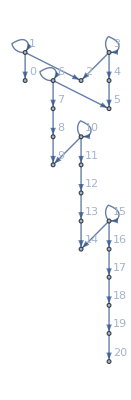

```mathematica
Graph[%112,VertexLabels->"Name"]
```

## Retry

```mathematica
l1={{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}};
```

```mathematica
rl1=
```